### Some constructed networks for Colton

```mathematica
Sort@Flatten@Table[{{x,y}->{x+1,y},{x,y}->{x,y+1}},{x,1,10},{y,1,10-x}]
```

{{1,1}→{1,2},{1,1}→{2,1},{1,2}→{1,3},{1,2}→{2,2},{1,3}→{1,4},{1,3}→{2,3},{1,4}→{1,5},{1,4}→{2,4},{1,5}→{1,6},{1,5}→{2,5},{1,6}→{1,7},{1,6}→{2,6},{1,7}→{1,8},{1,7}→{2,7},{1,8}→{1,9},{1,8}→{2,8},{1,9}→{1,10},{1,9}→{2,9},{2,1}→{2,2},{2,1}→{3,1},{2,2}→{2,3},{2,2}→{3,2},{2,3}→{2,4},{2,3}→{3,3},{2,4}→{2,5},{2,4}→{3,4},{2,5}→{2,6},{2,5}→{3,5},{2,6}→{2,7},{2,6}→{3,6},{2,7}→{2,8},{2,7}→{3,7},{2,8}→{2,9},{2,8}→{3,8},{3,1}→{3,2},{3,1}→{4,1},{3,2}→{3,3},{3,2}→{4,2},{3,3}→{3,4},{3,3}→{4,3},{3,4}→{3,5},{3,4}→{4,4},{3,5}→{3,6},{3,5}→{4,5},{3,6}→{3,7},{3,6}→{4,6},{3,7}→{3,8},{3,7}→{4,7},{4,1}→{4,2},{4,1}→{5,1},{4,2}→{4,3},{4,2}→{5,2},{4,3}→{4,4},{4,3}→{5,3},{4,4}→{4,5},{4,4}→{5,4},{4,5}→{4,6},{4,5}→{5,5},{4,6}→{4,7},{4,6}→{5,6},{5,1}→{5,2},{5,1}→{6,1},{5,2}→{5,3},{5,2}→{6,2},{5,3}→{5,4},{5,3}→{6,3},{5,4}→{5,5},{5,4}→{6,4},{5,5}→{5,6},{5,5}→{6,5},{6,1}→{6,2},{6,1}→{7,1},{6,2}→{6,3},{6,2}→{7,2},{6,3}→{6,4},{6,3}→{7,3},{6,4}→{6,5},{6,4}→{7,4},{7,1}→{7,2},{7,1}→{8,1},{7,2}→{7,3},{7,2}→{8,2},{7,3}→{7,4},{7,3}→{8,3},{8,1}→{8,2},{8,1}→{9,1},{8,2}→{8,3},{8,2}→{9,2},{9,1}→{9,2},{9,1}→{10,1}}

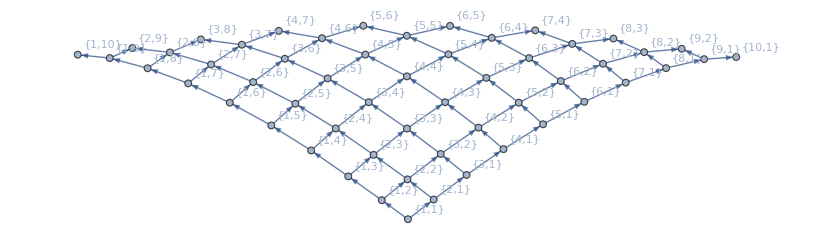

```mathematica
Graph[%, VertexLabels->"Name"]
```

```mathematica
net2dXY=Map[Reverse, Sort@Flatten@Table[{{x,y}->{x+1,y},{x,y}->{x,y+1}},{x,1,10},{y,1,10-x}] ,{2}]
```

{{1,1}→{2,1},{1,1}→{1,2},{2,1}→{3,1},{2,1}→{2,2},{3,1}→{4,1},{3,1}→{3,2},{4,1}→{5,1},{4,1}→{4,2},{5,1}→{6,1},{5,1}→{5,2},{6,1}→{7,1},{6,1}→{6,2},{7,1}→{8,1},{7,1}→{7,2},{8,1}→{9,1},{8,1}→{8,2},{9,1}→{10,1},{9,1}→{9,2},{1,2}→{2,2},{1,2}→{1,3},{2,2}→{3,2},{2,2}→{2,3},{3,2}→{4,2},{3,2}→{3,3},{4,2}→{5,2},{4,2}→{4,3},{5,2}→{6,2},{5,2}→{5,3},{6,2}→{7,2},{6,2}→{6,3},{7,2}→{8,2},{7,2}→{7,3},{8,2}→{9,2},{8,2}→{8,3},{1,3}→{2,3},{1,3}→{1,4},{2,3}→{3,3},{2,3}→{2,4},{3,3}→{4,3},{3,3}→{3,4},{4,3}→{5,3},{4,3}→{4,4},{5,3}→{6,3},{5,3}→{5,4},{6,3}→{7,3},{6,3}→{6,4},{7,3}→{8,3},{7,3}→{7,4},{1,4}→{2,4},{1,4}→{1,5},{2,4}→{3,4},{2,4}→{2,5},{3,4}→{4,4},{3,4}→{3,5},{4,4}→{5,4},{4,4}→{4,5},{5,4}→{6,4},{5,4}→{5,5},{6,4}→{7,4},{6,4}→{6,5},{1,5}→{2,5},{1,5}→{1,6},{2,5}→{3,5},{2,5}→{2,6},{3,5}→{4,5},{3,5}→{3,6},{4,5}→{5,5},{4,5}→{4,6},{5,5}→{6,5},{5,5}→{5,6},{1,6}→{2,6},{1,6}→{1,7},{2,6}→{3,6},{2,6}→{2,7},{3,6}→{4,6},{3,6}→{3,7},{4,6}→{5,6},{4,6}→{4,7},{1,7}→{2,7},{1,7}→{1,8},{2,7}→{3,7},{2,7}→{2,8},{3,7}→{4,7},{3,7}→{3,8},{1,8}→{2,8},{1,8}→{1,9},{2,8}→{3,8},{2,8}→{2,9},{1,9}→{2,9},{1,9}→{1,10}}

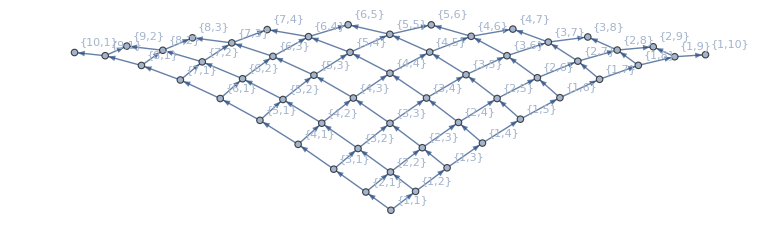

```mathematica
Graph[%,VertexLabels->"Name"]
```

```mathematica
Table[(n(n+1))/2,{n,1,10}]
```

{1,3,6,10,15,21,28,36,45,55}

```mathematica
net2dXY
```

{{1,1}→{2,1},{1,1}→{1,2},{2,1}→{3,1},{2,1}→{2,2},{3,1}→{4,1},{3,1}→{3,2},{4,1}→{5,1},{4,1}→{4,2},{5,1}→{6,1},{5,1}→{5,2},{6,1}→{7,1},{6,1}→{6,2},{7,1}→{8,1},{7,1}→{7,2},{8,1}→{9,1},{8,1}→{8,2},{9,1}→{10,1},{9,1}→{9,2},{1,2}→{2,2},{1,2}→{1,3},{2,2}→{3,2},{2,2}→{2,3},{3,2}→{4,2},{3,2}→{3,3},{4,2}→{5,2},{4,2}→{4,3},{5,2}→{6,2},{5,2}→{5,3},{6,2}→{7,2},{6,2}→{6,3},{7,2}→{8,2},{7,2}→{7,3},{8,2}→{9,2},{8,2}→{8,3},{1,3}→{2,3},{1,3}→{1,4},{2,3}→{3,3},{2,3}→{2,4},{3,3}→{4,3},{3,3}→{3,4},{4,3}→{5,3},{4,3}→{4,4},{5,3}→{6,3},{5,3}→{5,4},{6,3}→{7,3},{6,3}→{6,4},{7,3}→{8,3},{7,3}→{7,4},{1,4}→{2,4},{1,4}→{1,5},{2,4}→{3,4},{2,4}→{2,5},{3,4}→{4,4},{3,4}→{3,5},{4,4}→{5,4},{4,4}→{4,5},{5,4}→{6,4},{5,4}→{5,5},{6,4}→{7,4},{6,4}→{6,5},{1,5}→{2,5},{1,5}→{1,6},{2,5}→{3,5},{2,5}→{2,6},{3,5}→{4,5},{3,5}→{3,6},{4,5}→{5,5},{4,5}→{4,6},{5,5}→{6,5},{5,5}→{5,6},{1,6}→{2,6},{1,6}→{1,7},{2,6}→{3,6},{2,6}→{2,7},{3,6}→{4,6},{3,6}→{3,7},{4,6}→{5,6},{4,6}→{4,7},{1,7}→{2,7},{1,7}→{1,8},{2,7}→{3,7},{2,7}→{2,8},{3,7}→{4,7},{3,7}→{3,8},{1,8}→{2,8},{1,8}→{1,9},{2,8}→{3,8},{2,8}→{2,9},{1,9}→{2,9},{1,9}→{1,10}}

```mathematica
FullSimplify[(x+y-1)((x+y-1)+1)/2-(x-1)]//TraditionalForm
```

1/2 (x+y-1) (x+y)-x+1

```mathematica
net2dN = net2dXY/.{x_,y_} :> (x+y-1)(x+y)/2-x+1
```

{1→2,1→3,2→4,2→5,4→7,4→8,7→11,7→12,11→16,11→17,16→22,16→23,22→29,22→30,29→37,29→38,37→46,37→47,3→5,3→6,5→8,5→9,8→12,8→13,12→17,12→18,17→23,17→24,23→30,23→31,30→38,30→39,38→47,38→48,6→9,6→10,9→13,9→14,13→18,13→19,18→24,18→25,24→31,24→32,31→39,31→40,39→48,39→49,10→14,10→15,14→19,14→20,19→25,19→26,25→32,25→33,32→40,32→41,40→49,40→50,15→20,15→21,20→26,20→27,26→33,26→34,33→41,33→42,41→50,41→51,21→27,21→28,27→34,27→35,34→42,34→43,42→51,42→52,28→35,28→36,35→43,35→44,43→52,43→53,36→44,36→45,44→53,44→54,45→54,45→55}

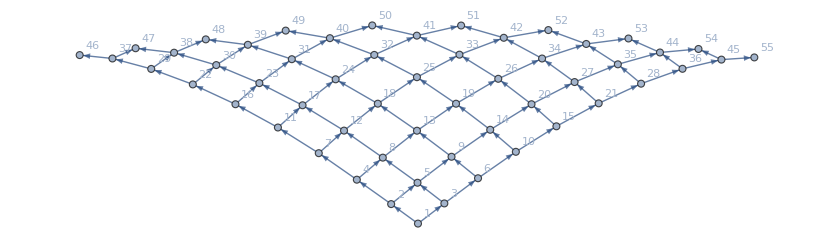

```mathematica
Graph[net2dN,VertexLabels->"Name"]
```

```mathematica
net2dN
```

{1→2,1→3,2→4,2→5,4→7,4→8,7→11,7→12,11→16,11→17,16→22,16→23,22→29,22→30,29→37,29→38,37→46,37→47,3→5,3→6,5→8,5→9,8→12,8→13,12→17,12→18,17→23,17→24,23→30,23→31,30→38,30→39,38→47,38→48,6→9,6→10,9→13,9→14,13→18,13→19,18→24,18→25,24→31,24→32,31→39,31→40,39→48,39→49,10→14,10→15,14→19,14→20,19→25,19→26,25→32,25→33,32→40,32→41,40→49,40→50,15→20,15→21,20→26,20→27,26→33,26→34,33→41,33→42,41→50,41→51,21→27,21→28,27→34,27→35,34→42,34→43,42→51,42→52,28→35,28→36,35→43,35→44,43→52,43→53,36→44,36→45,44→53,44→54,45→54,45→55}

```mathematica
ToNetDifferenceSets[net2dN]
```

{{1,2},{2,3},{2,3},{3,4},{3,4},{3,4},{4,5},{4,5},{4,5},{4,5},{5,6},{5,6},{5,6},{5,6},{5,6},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{7,8},{7,8},{7,8},{7,8},{7,8},{7,8},{7,8},{8,9},{8,9},{8,9},{8,9},{8,9},{8,9},{8,9},{8,9},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10}}

```mathematica
ToReducedNetDifferenceSets[{{1,2},{2,3},{2,3},{3,4},{3,4},{3,4},{4,5},{4,5},{4,5},{4,5},{5,6},{5,6},{5,6},{5,6},{5,6},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{7,8},{7,8},{7,8},{7,8},{7,8},{7,8},{7,8},{8,9},{8,9},{8,9},{8,9},{8,9},{8,9},{8,9},{8,9},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10}}]
```

{1·{{1,2}},2·{{2,3}},3·{{3,4}},4·{{4,5}},5·{{5,6}},6·{{6,7}},7·{{7,8}},8·{{8,9}},9·{{9,10}}}

```mathematica
ToReducedNetDifferenceSets[%]
```

```mathematica
{2 · {{2, 3}}, 3 · {{3, 4}}, 4 · {{4, 5}}, 5 · {{5, 6}}, 6 · {{6, 7}}, 7 · {{7, 8}}, 
 
  8 · {{8, 9}}, 9 · {{9, 10}}}
```

```mathematica
{1 · {{1, 2}}, 2 · {{2, 3}}, 3 · {{3, 4}}, 4 · {{4, 5}}, 5 · {{5, 6}}, 6 · {{6, 7}}, 
 
  7 · {{7, 8}}, 8 · {{8, 9}}}
```

Another attempt:

```mathematica
Tri[n_] := n(n+1)/2
```

```mathematica
net2dCantor = net2d/.{x_,y_} :> Tri[x+y-2]+y
```

{1→2,1→3,2→4,2→5,4→7,4→8,7→11,7→12,11→16,11→17,16→22,16→23,22→29,22→30,29→37,29→38,37→46,37→47,3→5,3→6,5→8,5→9,8→12,8→13,12→17,12→18,17→23,17→24,23→30,23→31,30→38,30→39,38→47,38→48,6→9,6→10,9→13,9→14,13→18,13→19,18→24,18→25,24→31,24→32,31→39,31→40,39→48,39→49,10→14,10→15,14→19,14→20,19→25,19→26,25→32,25→33,32→40,32→41,40→49,40→50,15→20,15→21,20→26,20→27,26→33,26→34,33→41,33→42,41→50,41→51,21→27,21→28,27→34,27→35,34→42,34→43,42→51,42→52,28→35,28→36,35→43,35→44,43→52,43→53,36→44,36→45,44→53,44→54,45→54,45→55}

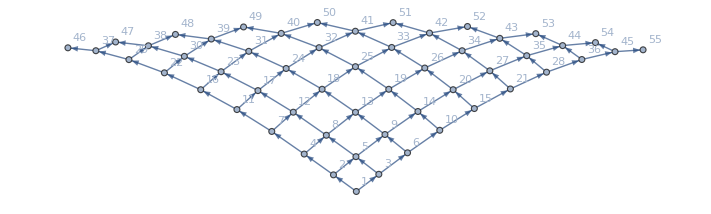

```mathematica
Graph[net2dCantor,VertexLabels->"Name"]
```

```mathematica
ToNetDifferenceSets@net2dCantor
```

{{1,2},{2,3},{2,3},{3,4},{3,4},{3,4},{4,5},{4,5},{4,5},{4,5},{5,6},{5,6},{5,6},{5,6},{5,6},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{7,8},{7,8},{7,8},{7,8},{7,8},{7,8},{7,8},{8,9},{8,9},{8,9},{8,9},{8,9},{8,9},{8,9},{8,9},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10}}

```mathematica
ToReducedNetDifferenceSets@ToNetDifferenceSets@net2dCantor
```

{1·{{1,2}},2·{{2,3}},3·{{3,4}},4·{{4,5}},5·{{5,6}},6·{{6,7}},7·{{7,8}},8·{{8,9}},9·{{9,10}}}

First difference row:

```mathematica
{1·{{1,1}},1·{{1,1}},1·{{1,1}},1·{{1,1}},1·{{1,1}},1·{{1,1}},1·{{1,1}},1·{{1,1}}}
```

Second difference row:

```mathematica
{0·{{0,0}},0·{{0,0}},0·{{0,0}},0·{{0,0}},0·{{0,0}},0·{{0,0}},0·{{0,0}},0·{{0,0}}}
```

Only 1 element of 0th & 1st difference rows needed to explain the pattern, since starting at 1, the 2nd difference row is all 0s.

Network ID  (number of rows needed:2 ⇒ 2-d):

({1·{{1,2}}}
{1·{{1,1}}})

Try another ordering:  by organic growth:

```mathematica
Clear[nextGen];
nextGen[{x_Integer,y_Integer}] := {{x,y}->{x+1,y},{x,y}->{x,y+1}};
nextGen[rl:{__Rule}] := Flatten[{rl,nextGen /@ Complement[ Last/@rl,Union[First/@ rl]]}];
nextGen[{1,1}]
```

{{1,1}→{2,1},{1,1}→{1,2}}

```mathematica
nextGen[%]
```

{{1,1}→{2,1},{1,1}→{1,2},{1,2}→{2,2},{1,2}→{1,3},{2,1}→{3,1},{2,1}→{2,2}}

```mathematica
net2dOrg=Nest[nextGen,{1,1},10]
```

{{1,1}→{2,1},{1,1}→{1,2},{1,2}→{2,2},{1,2}→{1,3},{2,1}→{3,1},{2,1}→{2,2},{1,3}→{2,3},{1,3}→{1,4},{2,2}→{3,2},{2,2}→{2,3},{3,1}→{4,1},{3,1}→{3,2},{1,4}→{2,4},{1,4}→{1,5},{2,3}→{3,3},{2,3}→{2,4},{3,2}→{4,2},{3,2}→{3,3},{4,1}→{5,1},{4,1}→{4,2},{1,5}→{2,5},{1,5}→{1,6},{2,4}→{3,4},{2,4}→{2,5},{3,3}→{4,3},{3,3}→{3,4},{4,2}→{5,2},{4,2}→{4,3},{5,1}→{6,1},{5,1}→{5,2},{1,6}→{2,6},{1,6}→{1,7},{2,5}→{3,5},{2,5}→{2,6},{3,4}→{4,4},{3,4}→{3,5},{4,3}→{5,3},{4,3}→{4,4},{5,2}→{6,2},{5,2}→{5,3},{6,1}→{7,1},{6,1}→{6,2},{1,7}→{2,7},{1,7}→{1,8},{2,6}→{3,6},{2,6}→{2,7},{3,5}→{4,5},{3,5}→{3,6},{4,4}→{5,4},{4,4}→{4,5},{5,3}→{6,3},{5,3}→{5,4},{6,2}→{7,2},{6,2}→{6,3},{7,1}→{8,1},{7,1}→{7,2},{1,8}→{2,8},{1,8}→{1,9},{2,7}→{3,7},{2,7}→{2,8},{3,6}→{4,6},{3,6}→{3,7},{4,5}→{5,5},{4,5}→{4,6},{5,4}→{6,4},{5,4}→{5,5},{6,3}→{7,3},{6,3}→{6,4},{7,2}→{8,2},{7,2}→{7,3},{8,1}→{9,1},{8,1}→{8,2},{1,9}→{2,9},{1,9}→{1,10},{2,8}→{3,8},{2,8}→{2,9},{3,7}→{4,7},{3,7}→{3,8},{4,6}→{5,6},{4,6}→{4,7},{5,5}→{6,5},{5,5}→{5,6},{6,4}→{7,4},{6,4}→{6,5},{7,3}→{8,3},{7,3}→{7,4},{8,2}→{9,2},{8,2}→{8,3},{9,1}→{10,1},{9,1}→{9,2},{1,10}→{2,10},{1,10}→{1,11},{2,9}→{3,9},{2,9}→{2,10},{3,8}→{4,8},{3,8}→{3,9},{4,7}→{5,7},{4,7}→{4,8},{5,6}→{6,6},{5,6}→{5,7},{6,5}→{7,5},{6,5}→{6,6},{7,4}→{8,4},{7,4}→{7,5},{8,3}→{9,3},{8,3}→{8,4},{9,2}→{10,2},{9,2}→{9,3},{10,1}→{11,1},{10,1}→{10,2}}

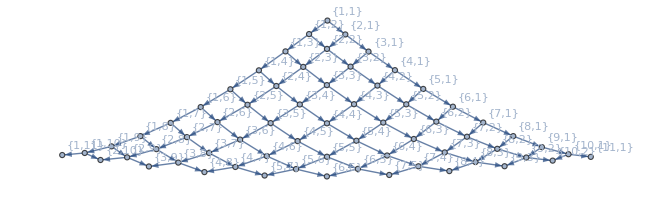

```mathematica
Graph[net2dOrg,VertexLabels->"Name"]
```

```mathematica
net2dOrgN=Sort[net2dOrg /. Thread[#->Range[Length[#]]]& @ DeleteDuplicates[Flatten[net2dOrg /. Rule->List,1]]]
```

{1→2,1→3,2→4,2→6,3→4,3→5,4→7,4→9,5→7,5→8,6→9,6→10,7→11,7→13,8→11,8→12,9→13,9→14,10→14,10→15,11→16,11→18,12→16,12→17,13→18,13→19,14→19,14→20,15→20,15→21,16→22,16→24,17→22,17→23,18→24,18→25,19→25,19→26,20→26,20→27,21→27,21→28,22→29,22→31,23→29,23→30,24→31,24→32,25→32,25→33,26→33,26→34,27→34,27→35,28→35,28→36,29→37,29→39,30→37,30→38,31→39,31→40,32→40,32→41,33→41,33→42,34→42,34→43,35→43,35→44,36→44,36→45,37→46,37→48,38→46,38→47,39→48,39→49,40→49,40→50,41→50,41→51,42→51,42→52,43→52,43→53,44→53,44→54,45→54,45→55,46→56,46→58,47→56,47→57,48→58,48→59,49→59,49→60,50→60,50→61,51→61,51→62,52→62,52→63,53→63,53→64,54→64,54→65,55→65,55→66}

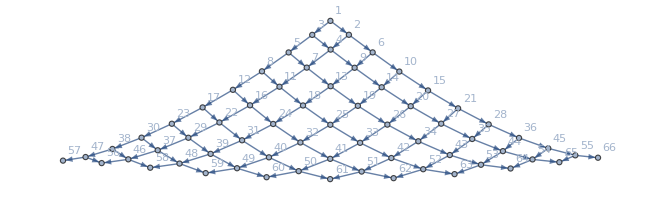

```mathematica
Graph[net2dOrgN,VertexLabels->"Name"]
```

```mathematica
ToNetDifferenceSets[net2dOrgN]
```

{{1,2},{2,4},{1,2},{3,5},{2,3},{3,4},{4,6},{3,4},{4,5},{4,5},{5,7},{4,5},{5,6},{5,6},{5,6},{6,8},{5,6},{6,7},{6,7},{6,7},{6,7},{7,9},{6,7},{7,8},{7,8},{7,8},{7,8},{7,8},{8,10},{7,8},{8,9},{8,9},{8,9},{8,9},{8,9},{8,9},{9,11},{8,9},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10},{10,12},{9,10},{10,11},{10,11},{10,11},{10,11},{10,11},{10,11},{10,11},{10,11}}

```mathematica
ToReducedNetDifferenceSets[%]
```

{1·{{1,2}},1·{{2,4}},1·{{1,2}},1·{{3,5}},1·{{2,3}},1·{{3,4}},1·{{4,6}},1·{{3,4}},2·{{4,5}},1·{{5,7}},1·{{4,5}},3·{{5,6}},1·{{6,8}},1·{{5,6}},4·{{6,7}},1·{{7,9}},1·{{6,7}},5·{{7,8}},1·{{8,10}},1·{{7,8}},6·{{8,9}},1·{{9,11}},1·{{8,9}},7·{{9,10}},1·{{10,12}},1·{{9,10}},8·{{10,11}}}

```mathematica
SetSubtract[%⟦4;;-1⟧,%⟦1;;-4⟧]
```

{0·{{2,3}},0·{{0,-1}},0·{{2,2}},0·{{1,1}},0·{{1,1}},1·{{1,1}},0·{{1,1}},0·{{1,1}},1·{{1,1}},0·{{1,1}},0·{{1,1}},1·{{1,1}},0·{{1,1}},0·{{1,1}},1·{{1,1}},0·{{1,1}},0·{{1,1}},1·{{1,1}},0·{{1,1}},0·{{1,1}},1·{{1,1}},0·{{1,1}},0·{{1,1}},1·{{1,1}}}

```mathematica
SetSubtract[%⟦4;;-1⟧,%⟦1;;-4⟧]
```

{0·{{-1,-2}},0·{{1,2}},1·{{-1,-1}},0·{{0,0}},0·{{0,0}},0·{{0,0}},0·{{0,0}},0·{{0,0}},0·{{0,0}},0·{{0,0}},0·{{0,0}},0·{{0,0}},0·{{0,0}},0·{{0,0}},0·{{0,0}},0·{{0,0}},0·{{0,0}},0·{{0,0}},0·{{0,0}},0·{{0,0}},0·{{0,0}}}

```mathematica
RecognizeNetDifferences[%]
```

0·{{1,2}} | 0·{{-1,-2}} | 0·{{2,3}} | 0·{{-1,-2}} | 0·{{1,1}} | 0·{{1,2}} | 0·{{-1,-2}} | 1·{{1,1}} | ∞ | 0·{{-1,-2}} | 2·{{1,1}} | ∞ | 0·{{-1,-2}} | 3·{{1,1}} | ∞ | 0·{{-1,-2}} | 4·{{1,1}}
0·{{0,0}} | 0·{{1,1}} | 0·{{1,1}} | 0·{{0,-1}} | 0·{{2,3}} | 0·{{0,0}} | 1·{{0,-1}} | 0·{{2,3}} | ∞ | 2·{{0,-1}} | 0·{{2,3}} | ∞ | 3·{{0,-1}} | 0·{{2,3}} | ∞ | 4·{{0,-1}} | 
0·{{2,3}} | 0·{{0,-1}} | 0·{{2,2}} | 0·{{1,1}} | 0·{{1,1}} | 1·{{1,1}} | 0·{{1,1}} | 0·{{1,1}} | 1·{{1,1}} | 0·{{1,1}} | 0·{{1,1}} | 1·{{1,1}} | 0·{{1,1}} | 0·{{1,1}} | 1·{{1,1}} |  | 
0·{{1,1}} | 0·{{1,0}} | 0·{{3,4}} | 0·{{0,-1}} | 1·{{2,2}} | 0·{{2,3}} | 0·{{0,-1}} | 2·{{2,2}} | ∞ | 0·{{0,-1}} | 3·{{2,2}} | ∞ | 0·{{0,-1}} | 4·{{2,2}} |  |  | 
0·{{2,2}} | 0·{{2,2}} | 0·{{2,2}} | 1·{{1,0}} | 0·{{3,4}} | 0·{{1,1}} | 2·{{1,0}} | 0·{{3,4}} | ∞ | 3·{{1,0}} | 0·{{3,4}} | ∞ | 4·{{1,0}} |  |  |  | 
0·{{3,4}} | 0·{{1,0}} | 1·{{3,3}} | 0·{{2,2}} | 0·{{2,2}} | 2·{{2,2}} | 0·{{2,2}} | 0·{{2,2}} | 2·{{2,2}} | 0·{{2,2}} | 0·{{2,2}} | 2·{{2,2}} |  |  |  |  | 
0·{{2,2}} | 1·{{2,1}} | 0·{{4,5}} | 0·{{1,0}} | 2·{{3,3}} | 0·{{3,4}} | 0·{{1,0}} | 3·{{3,3}} | ∞ | 0·{{1,0}} | 4·{{3,3}} |  |  |  |  |  | 
1·{{3,3}} | 0·{{3,3}} | 0·{{3,3}} | 2·{{2,1}} | 0·{{4,5}} | 0·{{2,2}} | 3·{{2,1}} | 0·{{4,5}} | ∞ | 4·{{2,1}} |  |  |  |  |  |  |

{count, offset, pattern, total}: {44,3,{0·{{2,3}},0·{{0,-1}},0·{{2,2}},0·{{1,1}},0·{{1,1}},1·{{1,1}},0·{{1,1}},0·{{1,1}},1·{{1,1}},0·{{1,1}},0·{{1,1}},1·{{1,1}},0·{{1,1}},0·{{1,1}},1·{{1,1}}},45}

{0,1,{{1,2}},17}

{97.7778%,{3,0,1,{{1,2}},17}}

```mathematica
RecognizeDifferenceRow[%]
```

{}

```mathematica
RecognizeNetSetDifferenceRow@%
```

{}

Move to 3-d:

```mathematica
net3d=Sort@Flatten@Table[{{x,y,z}->{x+1,y,z},{x,y,z}->{x,y+1,z},{x,y,z}->{x,y,z+1}},{x,1,15},{y,1,15-x},{z,1,15-x-y}]
```

{{1,1,1}→{1,1,2},{1,1,1}→{1,2,1},{1,1,1}→{2,1,1},{1,1,2}→{1,1,3},{1,1,2}→{1,2,2},{1,1,2}→{2,1,2},{1,1,3}→{1,1,4},{1,1,3}→{1,2,3},{1,1,3}→{2,1,3},{1,1,4}→{1,1,5},{1,1,4}→{1,2,4},{1,1,4}→{2,1,4},1342,{12,1,1}→{12,2,1},{12,1,1}→{13,1,1},{12,1,2}→{12,1,3},{12,1,2}→{12,2,2},{12,1,2}→{13,1,2},{12,2,1}→{12,2,2},{12,2,1}→{12,3,1},{12,2,1}→{13,2,1},{13,1,1}→{13,1,2},{13,1,1}→{13,2,1},{13,1,1}→{14,1,1}}
 |  |  |  |

$OutputSizeLimit::nosess: This output can only be updated in the same kernel session that generated it.

```mathematica
Graph3D[net3d]
```

-Graphics3D-

```mathematica
Select[net3d ,Plus @@ First[#]<5&]
```

{{1,1,1}→{1,1,2},{1,1,1}→{1,2,1},{1,1,1}→{2,1,1},{1,1,2}→{1,1,3},{1,1,2}→{1,2,2},{1,1,2}→{2,1,2},{1,2,1}→{1,2,2},{1,2,1}→{1,3,1},{1,2,1}→{2,2,1},{2,1,1}→{2,1,2},{2,1,1}→{2,2,1},{2,1,1}→{3,1,1}}

```mathematica
Plus@@(First@net3d[[1]])
```

3

```mathematica
Manipulate[Graph3D[Select[net3d ,Plus @@ First[#]<n&]],{n,4,11,1,Appearance}]
```

## 3d 1st octant triplets

```mathematica
name[{x_Integer,y_Integer,z_Integer}] := Module[{sum,slice,ss,σ, trisum},
sum=x+y+z;
slice=sum-2;
ss=slice-z+1;
σ=(ss-1)(ss)/2+y;
trisum=Sum[k(k+1)/2,{k,0,slice-1,1}];
Return[trisum+σ]
]
```

```mathematica
name[{2,2,1}]
```

9

```mathematica
Sum[k(k+1)/2,{k,0,n-1,1}]
```

1/6 (-1+n) n (1+n)

```mathematica
name/@{{1,1,1},{1,1,2},{2,1,1},{1,2,1},{1,1,3},{2,1,2},{1,2,2},{3,1,1},{2,2,1},{1,3,1},{1,1,4},{2,1,3},{1,2,3},{3,1,2},{2,2,2},{1,3,2},{4,1,1},{3,2,1},{2,3,1},{1,4,1},{1,1,5},{2,1,4},{1,2,4},{3,1,3},{2,2,3},{1,3,3},{4,1,2},{3,2,2},{2,3,2},{1,4,2},{5,1,1},{4,2,1},{3,3,1},{2,4,1},{1,5,1}}
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35}

```mathematica
%-Range[35]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
trisum+σ /. trisum->Sum[k(k+1)/2,{k,0,slice-1,1}]
```

1/6 (-1+slice) slice (1+slice)+σ

```mathematica
trisum+σ /. trisum->Sum[k(k+1)/2,{k,0,slice-1,1}] /. σ->(ss-1)(ss)/2+y
```

1/6 (-1+slice) slice (1+slice)+1/2 (-1+ss) ss+y

```mathematica
trisum+σ /. trisum->Sum[k(k+1)/2,{k,0,slice-1,1}] /. σ->(ss-1)(ss)/2+y /. ss->slice-z+1
```

1/6 (-1+slice) slice (1+slice)+y+1/2 (slice-z) (1+slice-z)

```mathematica
trisum+σ /. trisum->Sum[k(k+1)/2,{k,0,slice-1,1}] /. σ->(ss-1)(ss)/2+y /. ss->slice-z+1 /. slice->Σ-2//TraditionalForm
```

1/6 (Σ-3) (Σ-2) (Σ-1)+y+1/2 (Σ-z-2) (Σ-z-1)

```mathematica
trisum+σ /. trisum->Sum[k(k+1)/2,{k,0,slice-1,1}] /. σ->(ss-1)(ss)/2+y /. ss->slice-z+1 /. slice->sum-2 /. sum->x+y+z
```

y+1/2 (-2+x+y) (-1+x+y)+1/6 (-3+x+y+z) (-2+x+y+z) (-1+x+y+z)

```mathematica
FullSimplify[%]
```

y+1/2 (-2+x+y) (-1+x+y)+1/6 (-3+x+y+z) (-2+x+y+z) (-1+x+y+z)

```mathematica
net3dNamed =net3d /. {x_Integer,y_Integer,z_Integer} :> name[{x,y,z}]
```

{1→2,1→4,1→3,2→5,2→7,2→6,5→11,5→13,5→12,11→21,11→23,11→22,21→36,21→38,21→37,36→57,36→59,36→58,57→85,57→87,57→86,85→121,85→123,85→122,121→166,121→168,121→167,166→221,166→223,166→222,221→287,221→289,221→288,287→365,287→367,287→366,365→456,365→458,365→457,4→7,4→10,4→9,7→13,7→16,7→15,13→23,13→26,13→25,23→38,23→41,23→40,38→59,38→62,38→61,59→87,59→90,59→89,87→123,87→126,87→125,123→168,123→171,123→170,168→223,168→226,168→225,223→289,223→292,223→291,289→367,289→370,289→369,367→458,367→461,367→460,10→16,10→20,10→19,16→26,16→30,16→29,26→41,26→45,26→44,41→62,41→66,41→65,62→90,62→94,62→93,90→126,90→130,90→129,126→171,126→175,126→174,171→226,171→230,171→229,226→292,226→296,226→295,292→370,292→374,292→373,370→461,370→465,370→464,20→30,20→35,20→34,30→45,30→50,30→49,45→66,45→71,45→70,66→94,66→99,66→98,94→130,94→135,94→134,130→175,130→180,130→179,175→230,175→235,175→234,230→296,230→301,230→300,296→374,296→379,296→378,374→465,374→470,374→469,35→50,35→56,35→55,50→71,50→77,50→76,71→99,71→105,71→104,99→135,99→141,99→140,135→180,135→186,135→185,180→235,180→241,180→240,235→301,235→307,235→306,301→379,301→385,301→384,379→470,379→476,379→475,56→77,56→84,56→83,77→105,77→112,77→111,105→141,105→148,105→147,141→186,141→193,141→192,186→241,186→248,186→247,241→307,241→314,241→313,307→385,307→392,307→391,385→476,385→483,385→482,84→112,84→120,84→119,112→148,112→156,112→155,148→193,148→201,148→200,193→248,193→256,193→255,248→314,248→322,248→321,314→392,314→400,314→399,392→483,392→491,392→490,120→156,120→165,120→164,156→201,156→210,156→209,201→256,201→265,201→264,256→322,256→331,256→330,322→400,322→409,322→408,400→491,400→500,400→499,165→210,165→220,165→219,210→265,210→275,210→274,265→331,265→341,265→340,331→409,331→419,331→418,409→500,409→510,409→509,220→275,220→286,220→285,275→341,275→352,275→351,341→419,341→430,341→429,419→510,419→521,419→520,286→352,286→364,286→363,352→430,352→442,352→441,430→521,430→533,430→532,364→442,364→455,364→454,442→533,442→546,442→545,455→546,455→560,455→559,3→6,3→9,3→8,6→12,6→15,6→14,12→22,12→25,12→24,22→37,22→40,22→39,37→58,37→61,37→60,58→86,58→89,58→88,86→122,86→125,86→124,122→167,122→170,122→169,167→222,167→225,167→224,222→288,222→291,222→290,288→366,288→369,288→368,366→457,366→460,366→459,9→15,9→19,9→18,15→25,15→29,15→28,25→40,25→44,25→43,40→61,40→65,40→64,61→89,61→93,61→92,89→125,89→129,89→128,125→170,125→174,125→173,170→225,170→229,170→228,225→291,225→295,225→294,291→369,291→373,291→372,369→460,369→464,369→463,19→29,19→34,19→33,29→44,29→49,29→48,44→65,44→70,44→69,65→93,65→98,65→97,93→129,93→134,93→133,129→174,129→179,129→178,174→229,174→234,174→233,229→295,229→300,229→299,295→373,295→378,295→377,373→464,373→469,373→468,34→49,34→55,34→54,49→70,49→76,49→75,70→98,70→104,70→103,98→134,98→140,98→139,134→179,134→185,134→184,179→234,179→240,179→239,234→300,234→306,234→305,300→378,300→384,300→383,378→469,378→475,378→474,55→76,55→83,55→82,76→104,76→111,76→110,104→140,104→147,104→146,140→185,140→192,140→191,185→240,185→247,185→246,240→306,240→313,240→312,306→384,306→391,306→390,384→475,384→482,384→481,83→111,83→119,83→118,111→147,111→155,111→154,147→192,147→200,147→199,192→247,192→255,192→254,247→313,247→321,247→320,313→391,313→399,313→398,391→482,391→490,391→489,119→155,119→164,119→163,155→200,155→209,155→208,200→255,200→264,200→263,255→321,255→330,255→329,321→399,321→408,321→407,399→490,399→499,399→498,164→209,164→219,164→218,209→264,209→274,209→273,264→330,264→340,264→339,330→408,330→418,330→417,408→499,408→509,408→508,219→274,219→285,219→284,274→340,274→351,274→350,340→418,340→429,340→428,418→509,418→520,418→519,285→351,285→363,285→362,351→429,351→441,351→440,429→520,429→532,429→531,363→441,363→454,363→453,441→532,441→545,441→544,454→545,454→559,454→558,8→14,8→18,8→17,14→24,14→28,14→27,24→39,24→43,24→42,39→60,39→64,39→63,60→88,60→92,60→91,88→124,88→128,88→127,124→169,124→173,124→172,169→224,169→228,169→227,224→290,224→294,224→293,290→368,290→372,290→371,368→459,368→463,368→462,18→28,18→33,18→32,28→43,28→48,28→47,43→64,43→69,43→68,64→92,64→97,64→96,92→128,92→133,92→132,128→173,128→178,128→177,173→228,173→233,173→232,228→294,228→299,228→298,294→372,294→377,294→376,372→463,372→468,372→467,33→48,33→54,33→53,48→69,48→75,48→74,69→97,69→103,69→102,97→133,97→139,97→138,133→178,133→184,133→183,178→233,178→239,178→238,233→299,233→305,233→304,299→377,299→383,299→382,377→468,377→474,377→473,54→75,54→82,54→81,75→103,75→110,75→109,103→139,103→146,103→145,139→184,139→191,139→190,184→239,184→246,184→245,239→305,239→312,239→311,305→383,305→390,305→389,383→474,383→481,383→480,82→110,82→118,82→117,110→146,110→154,110→153,146→191,146→199,146→198,191→246,191→254,191→253,246→312,246→320,246→319,312→390,312→398,312→397,390→481,390→489,390→488,118→154,118→163,118→162,154→199,154→208,154→207,199→254,199→263,199→262,254→320,254→329,254→328,320→398,320→407,320→406,398→489,398→498,398→497,163→208,163→218,163→217,208→263,208→273,208→272,263→329,263→339,263→338,329→407,329→417,329→416,407→498,407→508,407→507,218→273,218→284,218→283,273→339,273→350,273→349,339→417,339→428,339→427,417→508,417→519,417→518,284→350,284→362,284→361,350→428,350→440,350→439,428→519,428→531,428→530,362→440,362→453,362→452,440→531,440→544,440→543,453→544,453→558,453→557,17→27,17→32,17→31,27→42,27→47,27→46,42→63,42→68,42→67,63→91,63→96,63→95,91→127,91→132,91→131,127→172,127→177,127→176,172→227,172→232,172→231,227→293,227→298,227→297,293→371,293→376,293→375,371→462,371→467,371→466,32→47,32→53,32→52,47→68,47→74,47→73,68→96,68→102,68→101,96→132,96→138,96→137,132→177,132→183,132→182,177→232,177→238,177→237,232→298,232→304,232→303,298→376,298→382,298→381,376→467,376→473,376→472,53→74,53→81,53→80,74→102,74→109,74→108,102→138,102→145,102→144,138→183,138→190,138→189,183→238,183→245,183→244,238→304,238→311,238→310,304→382,304→389,304→388,382→473,382→480,382→479,81→109,81→117,81→116,109→145,109→153,109→152,145→190,145→198,145→197,190→245,190→253,190→252,245→311,245→319,245→318,311→389,311→397,311→396,389→480,389→488,389→487,117→153,117→162,117→161,153→198,153→207,153→206,198→253,198→262,198→261,253→319,253→328,253→327,319→397,319→406,319→405,397→488,397→497,397→496,162→207,162→217,162→216,207→262,207→272,207→271,262→328,262→338,262→337,328→406,328→416,328→415,406→497,406→507,406→506,217→272,217→283,217→282,272→338,272→349,272→348,338→416,338→427,338→426,416→507,416→518,416→517,283→349,283→361,283→360,349→427,349→439,349→438,427→518,427→530,427→529,361→439,361→452,361→451,439→530,439→543,439→542,452→543,452→557,452→556,31→46,31→52,31→51,46→67,46→73,46→72,67→95,67→101,67→100,95→131,95→137,95→136,131→176,131→182,131→181,176→231,176→237,176→236,231→297,231→303,231→302,297→375,297→381,297→380,375→466,375→472,375→471,52→73,52→80,52→79,73→101,73→108,73→107,101→137,101→144,101→143,137→182,137→189,137→188,182→237,182→244,182→243,237→303,237→310,237→309,303→381,303→388,303→387,381→472,381→479,381→478,80→108,80→116,80→115,108→144,108→152,108→151,144→189,144→197,144→196,189→244,189→252,189→251,244→310,244→318,244→317,310→388,310→396,310→395,388→479,388→487,388→486,116→152,116→161,116→160,152→197,152→206,152→205,197→252,197→261,197→260,252→318,252→327,252→326,318→396,318→405,318→404,396→487,396→496,396→495,161→206,161→216,161→215,206→261,206→271,206→270,261→327,261→337,261→336,327→405,327→415,327→414,405→496,405→506,405→505,216→271,216→282,216→281,271→337,271→348,271→347,337→415,337→426,337→425,415→506,415→517,415→516,282→348,282→360,282→359,348→426,348→438,348→437,426→517,426→529,426→528,360→438,360→451,360→450,438→529,438→542,438→541,451→542,451→556,451→555,51→72,51→79,51→78,72→100,72→107,72→106,100→136,100→143,100→142,136→181,136→188,136→187,181→236,181→243,181→242,236→302,236→309,236→308,302→380,302→387,302→386,380→471,380→478,380→477,79→107,79→115,79→114,107→143,107→151,107→150,143→188,143→196,143→195,188→243,188→251,188→250,243→309,243→317,243→316,309→387,309→395,309→394,387→478,387→486,387→485,115→151,115→160,115→159,151→196,151→205,151→204,196→251,196→260,196→259,251→317,251→326,251→325,317→395,317→404,317→403,395→486,395→495,395→494,160→205,160→215,160→214,205→260,205→270,205→269,260→326,260→336,260→335,326→404,326→414,326→413,404→495,404→505,404→504,215→270,215→281,215→280,270→336,270→347,270→346,336→414,336→425,336→424,414→505,414→516,414→515,281→347,281→359,281→358,347→425,347→437,347→436,425→516,425→528,425→527,359→437,359→450,359→449,437→528,437→541,437→540,450→541,450→555,450→554,78→106,78→114,78→113,106→142,106→150,106→149,142→187,142→195,142→194,187→242,187→250,187→249,242→308,242→316,242→315,308→386,308→394,308→393,386→477,386→485,386→484,114→150,114→159,114→158,150→195,150→204,150→203,195→250,195→259,195→258,250→316,250→325,250→324,316→394,316→403,316→402,394→485,394→494,394→493,159→204,159→214,159→213,204→259,204→269,204→268,259→325,259→335,259→334,325→403,325→413,325→412,403→494,403→504,403→503,214→269,214→280,214→279,269→335,269→346,269→345,335→413,335→424,335→423,413→504,413→515,413→514,280→346,280→358,280→357,346→424,346→436,346→435,424→515,424→527,424→526,358→436,358→449,358→448,436→527,436→540,436→539,449→540,449→554,449→553,113→149,113→158,113→157,149→194,149→203,149→202,194→249,194→258,194→257,249→315,249→324,249→323,315→393,315→402,315→401,393→484,393→493,393→492,158→203,158→213,158→212,203→258,203→268,203→267,258→324,258→334,258→333,324→402,324→412,324→411,402→493,402→503,402→502,213→268,213→279,213→278,268→334,268→345,268→344,334→412,334→423,334→422,412→503,412→514,412→513,279→345,279→357,279→356,345→423,345→435,345→434,423→514,423→526,423→525,357→435,357→448,357→447,435→526,435→539,435→538,448→539,448→553,448→552,157→202,157→212,157→211,202→257,202→267,202→266,257→323,257→333,257→332,323→401,323→411,323→410,401→492,401→502,401→501,212→267,212→278,212→277,267→333,267→344,267→343,333→411,333→422,333→421,411→502,411→513,411→512,278→344,278→356,278→355,344→422,344→434,344→433,422→513,422→525,422→524,356→434,356→447,356→446,434→525,434→538,434→537,447→538,447→552,447→551,211→266,211→277,211→276,266→332,266→343,266→342,332→410,332→421,332→420,410→501,410→512,410→511,277→343,277→355,277→354,343→421,343→433,343→432,421→512,421→524,421→523,355→433,355→446,355→445,433→524,433→537,433→536,446→537,446→551,446→550,276→342,276→354,276→353,342→420,342→432,342→431,420→511,420→523,420→522,354→432,354→445,354→444,432→523,432→536,432→535,445→536,445→550,445→549,353→431,353→444,353→443,431→522,431→535,431→534,444→535,444→549,444→548,443→534,443→548,443→547}

```mathematica
Sort[{1->2,1->4,1->3,2->5,2->7,2->6,5->11,5->13,5->12,11->21,11->23,11->22,21->36,21->38,21->37,36->57,36->59,36->58,57->85,57->87,57->86,85->121,85->123,85->122,121->166,121->168,121->167,166->221,166->223,166->222,221->287,221->289,221->288,287->365,287->367,287->366,365->456,365->458,365->457,4->7,4->10,4->9,7->13,7->16,7->15,13->23,13->26,13->25,23->38,23->41,23->40,38->59,38->62,38->61,59->87,59->90,59->89,87->123,87->126,87->125,123->168,123->171,123->170,168->223,168->226,168->225,223->289,223->292,223->291,289->367,289->370,289->369,367->458,367->461,367->460,10->16,10->20,10->19,16->26,16->30,16->29,26->41,26->45,26->44,41->62,41->66,41->65,62->90,62->94,62->93,90->126,90->130,90->129,126->171,126->175,126->174,171->226,171->230,171->229,226->292,226->296,226->295,292->370,292->374,292->373,370->461,370->465,370->464,20->30,20->35,20->34,30->45,30->50,30->49,45->66,45->71,45->70,66->94,66->99,66->98,94->130,94->135,94->134,130->175,130->180,130->179,175->230,175->235,175->234,230->296,230->301,230->300,296->374,296->379,296->378,374->465,374->470,374->469,35->50,35->56,35->55,50->71,50->77,50->76,71->99,71->105,71->104,99->135,99->141,99->140,135->180,135->186,135->185,180->235,180->241,180->240,235->301,235->307,235->306,301->379,301->385,301->384,379->470,379->476,379->475,56->77,56->84,56->83,77->105,77->112,77->111,105->141,105->148,105->147,141->186,141->193,141->192,186->241,186->248,186->247,241->307,241->314,241->313,307->385,307->392,307->391,385->476,385->483,385->482,84->112,84->120,84->119,112->148,112->156,112->155,148->193,148->201,148->200,193->248,193->256,193->255,248->314,248->322,248->321,314->392,314->400,314->399,392->483,392->491,392->490,120->156,120->165,120->164,156->201,156->210,156->209,201->256,201->265,201->264,256->322,256->331,256->330,322->400,322->409,322->408,400->491,400->500,400->499,165->210,165->220,165->219,210->265,210->275,210->274,265->331,265->341,265->340,331->409,331->419,331->418,409->500,409->510,409->509,220->275,220->286,220->285,275->341,275->352,275->351,341->419,341->430,341->429,419->510,419->521,419->520,286->352,286->364,286->363,352->430,352->442,352->441,430->521,430->533,430->532,364->442,364->455,364->454,442->533,442->546,442->545,455->546,455->560,455->559,3->6,3->9,3->8,6->12,6->15,6->14,12->22,12->25,12->24,22->37,22->40,22->39,37->58,37->61,37->60,58->86,58->89,58->88,86->122,86->125,86->124,122->167,122->170,122->169,167->222,167->225,167->224,222->288,222->291,222->290,288->366,288->369,288->368,366->457,366->460,366->459,9->15,9->19,9->18,15->25,15->29,15->28,25->40,25->44,25->43,40->61,40->65,40->64,61->89,61->93,61->92,89->125,89->129,89->128,125->170,125->174,125->173,170->225,170->229,170->228,225->291,225->295,225->294,291->369,291->373,291->372,369->460,369->464,369->463,19->29,19->34,19->33,29->44,29->49,29->48,44->65,44->70,44->69,65->93,65->98,65->97,93->129,93->134,93->133,129->174,129->179,129->178,174->229,174->234,174->233,229->295,229->300,229->299,295->373,295->378,295->377,373->464,373->469,373->468,34->49,34->55,34->54,49->70,49->76,49->75,70->98,70->104,70->103,98->134,98->140,98->139,134->179,134->185,134->184,179->234,179->240,179->239,234->300,234->306,234->305,300->378,300->384,300->383,378->469,378->475,378->474,55->76,55->83,55->82,76->104,76->111,76->110,104->140,104->147,104->146,140->185,140->192,140->191,185->240,185->247,185->246,240->306,240->313,240->312,306->384,306->391,306->390,384->475,384->482,384->481,83->111,83->119,83->118,111->147,111->155,111->154,147->192,147->200,147->199,192->247,192->255,192->254,247->313,247->321,247->320,313->391,313->399,313->398,391->482,391->490,391->489,119->155,119->164,119->163,155->200,155->209,155->208,200->255,200->264,200->263,255->321,255->330,255->329,321->399,321->408,321->407,399->490,399->499,399->498,164->209,164->219,164->218,209->264,209->274,209->273,264->330,264->340,264->339,330->408,330->418,330->417,408->499,408->509,408->508,219->274,219->285,219->284,274->340,274->351,274->350,340->418,340->429,340->428,418->509,418->520,418->519,285->351,285->363,285->362,351->429,351->441,351->440,429->520,429->532,429->531,363->441,363->454,363->453,441->532,441->545,441->544,454->545,454->559,454->558,8->14,8->18,8->17,14->24,14->28,14->27,24->39,24->43,24->42,39->60,39->64,39->63,60->88,60->92,60->91,88->124,88->128,88->127,124->169,124->173,124->172,169->224,169->228,169->227,224->290,224->294,224->293,290->368,290->372,290->371,368->459,368->463,368->462,18->28,18->33,18->32,28->43,28->48,28->47,43->64,43->69,43->68,64->92,64->97,64->96,92->128,92->133,92->132,128->173,128->178,128->177,173->228,173->233,173->232,228->294,228->299,228->298,294->372,294->377,294->376,372->463,372->468,372->467,33->48,33->54,33->53,48->69,48->75,48->74,69->97,69->103,69->102,97->133,97->139,97->138,133->178,133->184,133->183,178->233,178->239,178->238,233->299,233->305,233->304,299->377,299->383,299->382,377->468,377->474,377->473,54->75,54->82,54->81,75->103,75->110,75->109,103->139,103->146,103->145,139->184,139->191,139->190,184->239,184->246,184->245,239->305,239->312,239->311,305->383,305->390,305->389,383->474,383->481,383->480,82->110,82->118,82->117,110->146,110->154,110->153,146->191,146->199,146->198,191->246,191->254,191->253,246->312,246->320,246->319,312->390,312->398,312->397,390->481,390->489,390->488,118->154,118->163,118->162,154->199,154->208,154->207,199->254,199->263,199->262,254->320,254->329,254->328,320->398,320->407,320->406,398->489,398->498,398->497,163->208,163->218,163->217,208->263,208->273,208->272,263->329,263->339,263->338,329->407,329->417,329->416,407->498,407->508,407->507,218->273,218->284,218->283,273->339,273->350,273->349,339->417,339->428,339->427,417->508,417->519,417->518,284->350,284->362,284->361,350->428,350->440,350->439,428->519,428->531,428->530,362->440,362->453,362->452,440->531,440->544,440->543,453->544,453->558,453->557,17->27,17->32,17->31,27->42,27->47,27->46,42->63,42->68,42->67,63->91,63->96,63->95,91->127,91->132,91->131,127->172,127->177,127->176,172->227,172->232,172->231,227->293,227->298,227->297,293->371,293->376,293->375,371->462,371->467,371->466,32->47,32->53,32->52,47->68,47->74,47->73,68->96,68->102,68->101,96->132,96->138,96->137,132->177,132->183,132->182,177->232,177->238,177->237,232->298,232->304,232->303,298->376,298->382,298->381,376->467,376->473,376->472,53->74,53->81,53->80,74->102,74->109,74->108,102->138,102->145,102->144,138->183,138->190,138->189,183->238,183->245,183->244,238->304,238->311,238->310,304->382,304->389,304->388,382->473,382->480,382->479,81->109,81->117,81->116,109->145,109->153,109->152,145->190,145->198,145->197,190->245,190->253,190->252,245->311,245->319,245->318,311->389,311->397,311->396,389->480,389->488,389->487,117->153,117->162,117->161,153->198,153->207,153->206,198->253,198->262,198->261,253->319,253->328,253->327,319->397,319->406,319->405,397->488,397->497,397->496,162->207,162->217,162->216,207->262,207->272,207->271,262->328,262->338,262->337,328->406,328->416,328->415,406->497,406->507,406->506,217->272,217->283,217->282,272->338,272->349,272->348,338->416,338->427,338->426,416->507,416->518,416->517,283->349,283->361,283->360,349->427,349->439,349->438,427->518,427->530,427->529,361->439,361->452,361->451,439->530,439->543,439->542,452->543,452->557,452->556,31->46,31->52,31->51,46->67,46->73,46->72,67->95,67->101,67->100,95->131,95->137,95->136,131->176,131->182,131->181,176->231,176->237,176->236,231->297,231->303,231->302,297->375,297->381,297->380,375->466,375->472,375->471,52->73,52->80,52->79,73->101,73->108,73->107,101->137,101->144,101->143,137->182,137->189,137->188,182->237,182->244,182->243,237->303,237->310,237->309,303->381,303->388,303->387,381->472,381->479,381->478,80->108,80->116,80->115,108->144,108->152,108->151,144->189,144->197,144->196,189->244,189->252,189->251,244->310,244->318,244->317,310->388,310->396,310->395,388->479,388->487,388->486,116->152,116->161,116->160,152->197,152->206,152->205,197->252,197->261,197->260,252->318,252->327,252->326,318->396,318->405,318->404,396->487,396->496,396->495,161->206,161->216,161->215,206->261,206->271,206->270,261->327,261->337,261->336,327->405,327->415,327->414,405->496,405->506,405->505,216->271,216->282,216->281,271->337,271->348,271->347,337->415,337->426,337->425,415->506,415->517,415->516,282->348,282->360,282->359,348->426,348->438,348->437,426->517,426->529,426->528,360->438,360->451,360->450,438->529,438->542,438->541,451->542,451->556,451->555,51->72,51->79,51->78,72->100,72->107,72->106,100->136,100->143,100->142,136->181,136->188,136->187,181->236,181->243,181->242,236->302,236->309,236->308,302->380,302->387,302->386,380->471,380->478,380->477,79->107,79->115,79->114,107->143,107->151,107->150,143->188,143->196,143->195,188->243,188->251,188->250,243->309,243->317,243->316,309->387,309->395,309->394,387->478,387->486,387->485,115->151,115->160,115->159,151->196,151->205,151->204,196->251,196->260,196->259,251->317,251->326,251->325,317->395,317->404,317->403,395->486,395->495,395->494,160->205,160->215,160->214,205->260,205->270,205->269,260->326,260->336,260->335,326->404,326->414,326->413,404->495,404->505,404->504,215->270,215->281,215->280,270->336,270->347,270->346,336->414,336->425,336->424,414->505,414->516,414->515,281->347,281->359,281->358,347->425,347->437,347->436,425->516,425->528,425->527,359->437,359->450,359->449,437->528,437->541,437->540,450->541,450->555,450->554,78->106,78->114,78->113,106->142,106->150,106->149,142->187,142->195,142->194,187->242,187->250,187->249,242->308,242->316,242->315,308->386,308->394,308->393,386->477,386->485,386->484,114->150,114->159,114->158,150->195,150->204,150->203,195->250,195->259,195->258,250->316,250->325,250->324,316->394,316->403,316->402,394->485,394->494,394->493,159->204,159->214,159->213,204->259,204->269,204->268,259->325,259->335,259->334,325->403,325->413,325->412,403->494,403->504,403->503,214->269,214->280,214->279,269->335,269->346,269->345,335->413,335->424,335->423,413->504,413->515,413->514,280->346,280->358,280->357,346->424,346->436,346->435,424->515,424->527,424->526,358->436,358->449,358->448,436->527,436->540,436->539,449->540,449->554,449->553,113->149,113->158,113->157,149->194,149->203,149->202,194->249,194->258,194->257,249->315,249->324,249->323,315->393,315->402,315->401,393->484,393->493,393->492,158->203,158->213,158->212,203->258,203->268,203->267,258->324,258->334,258->333,324->402,324->412,324->411,402->493,402->503,402->502,213->268,213->279,213->278,268->334,268->345,268->344,334->412,334->423,334->422,412->503,412->514,412->513,279->345,279->357,279->356,345->423,345->435,345->434,423->514,423->526,423->525,357->435,357->448,357->447,435->526,435->539,435->538,448->539,448->553,448->552,157->202,157->212,157->211,202->257,202->267,202->266,257->323,257->333,257->332,323->401,323->411,323->410,401->492,401->502,401->501,212->267,212->278,212->277,267->333,267->344,267->343,333->411,333->422,333->421,411->502,411->513,411->512,278->344,278->356,278->355,344->422,344->434,344->433,422->513,422->525,422->524,356->434,356->447,356->446,434->525,434->538,434->537,447->538,447->552,447->551,211->266,211->277,211->276,266->332,266->343,266->342,332->410,332->421,332->420,410->501,410->512,410->511,277->343,277->355,277->354,343->421,343->433,343->432,421->512,421->524,421->523,355->433,355->446,355->445,433->524,433->537,433->536,446->537,446->551,446->550,276->342,276->354,276->353,342->420,342->432,342->431,420->511,420->523,420->522,354->432,354->445,354->444,432->523,432->536,432->535,445->536,445->550,445->549,353->431,353->444,353->443,431->522,431->535,431->534,444->535,444->549,444->548,443->534,443->548,443->547}]
```

{1→2,1→3,1→4,2→5,2→6,2→7,3→6,3→8,3→9,4→7,4→9,4→10,5→11,5→12,5→13,6→12,6→14,6→15,7→13,7→15,7→16,8→14,8→17,8→18,9→15,9→18,9→19,10→16,10→19,10→20,11→21,11→22,11→23,12→22,12→24,12→25,13→23,13→25,13→26,14→24,14→27,14→28,15→25,15→28,15→29,16→26,16→29,16→30,17→27,17→31,17→32,18→28,18→32,18→33,19→29,19→33,19→34,20→30,20→34,20→35,21→36,21→37,21→38,22→37,22→39,22→40,23→38,23→40,23→41,24→39,24→42,24→43,25→40,25→43,25→44,26→41,26→44,26→45,27→42,27→46,27→47,28→43,28→47,28→48,29→44,29→48,29→49,30→45,30→49,30→50,31→46,31→51,31→52,32→47,32→52,32→53,33→48,33→53,33→54,34→49,34→54,34→55,35→50,35→55,35→56,36→57,36→58,36→59,37→58,37→60,37→61,38→59,38→61,38→62,39→60,39→63,39→64,40→61,40→64,40→65,41→62,41→65,41→66,42→63,42→67,42→68,43→64,43→68,43→69,44→65,44→69,44→70,45→66,45→70,45→71,46→67,46→72,46→73,47→68,47→73,47→74,48→69,48→74,48→75,49→70,49→75,49→76,50→71,50→76,50→77,51→72,51→78,51→79,52→73,52→79,52→80,53→74,53→80,53→81,54→75,54→81,54→82,55→76,55→82,55→83,56→77,56→83,56→84,57→85,57→86,57→87,58→86,58→88,58→89,59→87,59→89,59→90,60→88,60→91,60→92,61→89,61→92,61→93,62→90,62→93,62→94,63→91,63→95,63→96,64→92,64→96,64→97,65→93,65→97,65→98,66→94,66→98,66→99,67→95,67→100,67→101,68→96,68→101,68→102,69→97,69→102,69→103,70→98,70→103,70→104,71→99,71→104,71→105,72→100,72→106,72→107,73→101,73→107,73→108,74→102,74→108,74→109,75→103,75→109,75→110,76→104,76→110,76→111,77→105,77→111,77→112,78→106,78→113,78→114,79→107,79→114,79→115,80→108,80→115,80→116,81→109,81→116,81→117,82→110,82→117,82→118,83→111,83→118,83→119,84→112,84→119,84→120,85→121,85→122,85→123,86→122,86→124,86→125,87→123,87→125,87→126,88→124,88→127,88→128,89→125,89→128,89→129,90→126,90→129,90→130,91→127,91→131,91→132,92→128,92→132,92→133,93→129,93→133,93→134,94→130,94→134,94→135,95→131,95→136,95→137,96→132,96→137,96→138,97→133,97→138,97→139,98→134,98→139,98→140,99→135,99→140,99→141,100→136,100→142,100→143,101→137,101→143,101→144,102→138,102→144,102→145,103→139,103→145,103→146,104→140,104→146,104→147,105→141,105→147,105→148,106→142,106→149,106→150,107→143,107→150,107→151,108→144,108→151,108→152,109→145,109→152,109→153,110→146,110→153,110→154,111→147,111→154,111→155,112→148,112→155,112→156,113→149,113→157,113→158,114→150,114→158,114→159,115→151,115→159,115→160,116→152,116→160,116→161,117→153,117→161,117→162,118→154,118→162,118→163,119→155,119→163,119→164,120→156,120→164,120→165,121→166,121→167,121→168,122→167,122→169,122→170,123→168,123→170,123→171,124→169,124→172,124→173,125→170,125→173,125→174,126→171,126→174,126→175,127→172,127→176,127→177,128→173,128→177,128→178,129→174,129→178,129→179,130→175,130→179,130→180,131→176,131→181,131→182,132→177,132→182,132→183,133→178,133→183,133→184,134→179,134→184,134→185,135→180,135→185,135→186,136→181,136→187,136→188,137→182,137→188,137→189,138→183,138→189,138→190,139→184,139→190,139→191,140→185,140→191,140→192,141→186,141→192,141→193,142→187,142→194,142→195,143→188,143→195,143→196,144→189,144→196,144→197,145→190,145→197,145→198,146→191,146→198,146→199,147→192,147→199,147→200,148→193,148→200,148→201,149→194,149→202,149→203,150→195,150→203,150→204,151→196,151→204,151→205,152→197,152→205,152→206,153→198,153→206,153→207,154→199,154→207,154→208,155→200,155→208,155→209,156→201,156→209,156→210,157→202,157→211,157→212,158→203,158→212,158→213,159→204,159→213,159→214,160→205,160→214,160→215,161→206,161→215,161→216,162→207,162→216,162→217,163→208,163→217,163→218,164→209,164→218,164→219,165→210,165→219,165→220,166→221,166→222,166→223,167→222,167→224,167→225,168→223,168→225,168→226,169→224,169→227,169→228,170→225,170→228,170→229,171→226,171→229,171→230,172→227,172→231,172→232,173→228,173→232,173→233,174→229,174→233,174→234,175→230,175→234,175→235,176→231,176→236,176→237,177→232,177→237,177→238,178→233,178→238,178→239,179→234,179→239,179→240,180→235,180→240,180→241,181→236,181→242,181→243,182→237,182→243,182→244,183→238,183→244,183→245,184→239,184→245,184→246,185→240,185→246,185→247,186→241,186→247,186→248,187→242,187→249,187→250,188→243,188→250,188→251,189→244,189→251,189→252,190→245,190→252,190→253,191→246,191→253,191→254,192→247,192→254,192→255,193→248,193→255,193→256,194→249,194→257,194→258,195→250,195→258,195→259,196→251,196→259,196→260,197→252,197→260,197→261,198→253,198→261,198→262,199→254,199→262,199→263,200→255,200→263,200→264,201→256,201→264,201→265,202→257,202→266,202→267,203→258,203→267,203→268,204→259,204→268,204→269,205→260,205→269,205→270,206→261,206→270,206→271,207→262,207→271,207→272,208→263,208→272,208→273,209→264,209→273,209→274,210→265,210→274,210→275,211→266,211→276,211→277,212→267,212→277,212→278,213→268,213→278,213→279,214→269,214→279,214→280,215→270,215→280,215→281,216→271,216→281,216→282,217→272,217→282,217→283,218→273,218→283,218→284,219→274,219→284,219→285,220→275,220→285,220→286,221→287,221→288,221→289,222→288,222→290,222→291,223→289,223→291,223→292,224→290,224→293,224→294,225→291,225→294,225→295,226→292,226→295,226→296,227→293,227→297,227→298,228→294,228→298,228→299,229→295,229→299,229→300,230→296,230→300,230→301,231→297,231→302,231→303,232→298,232→303,232→304,233→299,233→304,233→305,234→300,234→305,234→306,235→301,235→306,235→307,236→302,236→308,236→309,237→303,237→309,237→310,238→304,238→310,238→311,239→305,239→311,239→312,240→306,240→312,240→313,241→307,241→313,241→314,242→308,242→315,242→316,243→309,243→316,243→317,244→310,244→317,244→318,245→311,245→318,245→319,246→312,246→319,246→320,247→313,247→320,247→321,248→314,248→321,248→322,249→315,249→323,249→324,250→316,250→324,250→325,251→317,251→325,251→326,252→318,252→326,252→327,253→319,253→327,253→328,254→320,254→328,254→329,255→321,255→329,255→330,256→322,256→330,256→331,257→323,257→332,257→333,258→324,258→333,258→334,259→325,259→334,259→335,260→326,260→335,260→336,261→327,261→336,261→337,262→328,262→337,262→338,263→329,263→338,263→339,264→330,264→339,264→340,265→331,265→340,265→341,266→332,266→342,266→343,267→333,267→343,267→344,268→334,268→344,268→345,269→335,269→345,269→346,270→336,270→346,270→347,271→337,271→347,271→348,272→338,272→348,272→349,273→339,273→349,273→350,274→340,274→350,274→351,275→341,275→351,275→352,276→342,276→353,276→354,277→343,277→354,277→355,278→344,278→355,278→356,279→345,279→356,279→357,280→346,280→357,280→358,281→347,281→358,281→359,282→348,282→359,282→360,283→349,283→360,283→361,284→350,284→361,284→362,285→351,285→362,285→363,286→352,286→363,286→364,287→365,287→366,287→367,288→366,288→368,288→369,289→367,289→369,289→370,290→368,290→371,290→372,291→369,291→372,291→373,292→370,292→373,292→374,293→371,293→375,293→376,294→372,294→376,294→377,295→373,295→377,295→378,296→374,296→378,296→379,297→375,297→380,297→381,298→376,298→381,298→382,299→377,299→382,299→383,300→378,300→383,300→384,301→379,301→384,301→385,302→380,302→386,302→387,303→381,303→387,303→388,304→382,304→388,304→389,305→383,305→389,305→390,306→384,306→390,306→391,307→385,307→391,307→392,308→386,308→393,308→394,309→387,309→394,309→395,310→388,310→395,310→396,311→389,311→396,311→397,312→390,312→397,312→398,313→391,313→398,313→399,314→392,314→399,314→400,315→393,315→401,315→402,316→394,316→402,316→403,317→395,317→403,317→404,318→396,318→404,318→405,319→397,319→405,319→406,320→398,320→406,320→407,321→399,321→407,321→408,322→400,322→408,322→409,323→401,323→410,323→411,324→402,324→411,324→412,325→403,325→412,325→413,326→404,326→413,326→414,327→405,327→414,327→415,328→406,328→415,328→416,329→407,329→416,329→417,330→408,330→417,330→418,331→409,331→418,331→419,332→410,332→420,332→421,333→411,333→421,333→422,334→412,334→422,334→423,335→413,335→423,335→424,336→414,336→424,336→425,337→415,337→425,337→426,338→416,338→426,338→427,339→417,339→427,339→428,340→418,340→428,340→429,341→419,341→429,341→430,342→420,342→431,342→432,343→421,343→432,343→433,344→422,344→433,344→434,345→423,345→434,345→435,346→424,346→435,346→436,347→425,347→436,347→437,348→426,348→437,348→438,349→427,349→438,349→439,350→428,350→439,350→440,351→429,351→440,351→441,352→430,352→441,352→442,353→431,353→443,353→444,354→432,354→444,354→445,355→433,355→445,355→446,356→434,356→446,356→447,357→435,357→447,357→448,358→436,358→448,358→449,359→437,359→449,359→450,360→438,360→450,360→451,361→439,361→451,361→452,362→440,362→452,362→453,363→441,363→453,363→454,364→442,364→454,364→455,365→456,365→457,365→458,366→457,366→459,366→460,367→458,367→460,367→461,368→459,368→462,368→463,369→460,369→463,369→464,370→461,370→464,370→465,371→462,371→466,371→467,372→463,372→467,372→468,373→464,373→468,373→469,374→465,374→469,374→470,375→466,375→471,375→472,376→467,376→472,376→473,377→468,377→473,377→474,378→469,378→474,378→475,379→470,379→475,379→476,380→471,380→477,380→478,381→472,381→478,381→479,382→473,382→479,382→480,383→474,383→480,383→481,384→475,384→481,384→482,385→476,385→482,385→483,386→477,386→484,386→485,387→478,387→485,387→486,388→479,388→486,388→487,389→480,389→487,389→488,390→481,390→488,390→489,391→482,391→489,391→490,392→483,392→490,392→491,393→484,393→492,393→493,394→485,394→493,394→494,395→486,395→494,395→495,396→487,396→495,396→496,397→488,397→496,397→497,398→489,398→497,398→498,399→490,399→498,399→499,400→491,400→499,400→500,401→492,401→501,401→502,402→493,402→502,402→503,403→494,403→503,403→504,404→495,404→504,404→505,405→496,405→505,405→506,406→497,406→506,406→507,407→498,407→507,407→508,408→499,408→508,408→509,409→500,409→509,409→510,410→501,410→511,410→512,411→502,411→512,411→513,412→503,412→513,412→514,413→504,413→514,413→515,414→505,414→515,414→516,415→506,415→516,415→517,416→507,416→517,416→518,417→508,417→518,417→519,418→509,418→519,418→520,419→510,419→520,419→521,420→511,420→522,420→523,421→512,421→523,421→524,422→513,422→524,422→525,423→514,423→525,423→526,424→515,424→526,424→527,425→516,425→527,425→528,426→517,426→528,426→529,427→518,427→529,427→530,428→519,428→530,428→531,429→520,429→531,429→532,430→521,430→532,430→533,431→522,431→534,431→535,432→523,432→535,432→536,433→524,433→536,433→537,434→525,434→537,434→538,435→526,435→538,435→539,436→527,436→539,436→540,437→528,437→540,437→541,438→529,438→541,438→542,439→530,439→542,439→543,440→531,440→543,440→544,441→532,441→544,441→545,442→533,442→545,442→546,443→534,443→547,443→548,444→535,444→548,444→549,445→536,445→549,445→550,446→537,446→550,446→551,447→538,447→551,447→552,448→539,448→552,448→553,449→540,449→553,449→554,450→541,450→554,450→555,451→542,451→555,451→556,452→543,452→556,452→557,453→544,453→557,453→558,454→545,454→558,454→559,455→546,455→559,455→560}

```mathematica
ToNetDifferenceSets[%135]
```

{{1,2,3},{3,4,5},{3,5,6},{3,5,6},{6,7,8},{6,8,9},{6,8,9},{6,9,10},{6,9,10},{6,9,10},{10,11,12},{10,12,13},{10,12,13},{10,13,14},{10,13,14},{10,13,14},{10,14,15},{10,14,15},{10,14,15},{10,14,15},{15,16,17},{15,17,18},{15,17,18},{15,18,19},{15,18,19},{15,18,19},{15,19,20},{15,19,20},{15,19,20},{15,19,20},{15,20,21},{15,20,21},{15,20,21},{15,20,21},{15,20,21},{21,22,23},{21,23,24},{21,23,24},{21,24,25},{21,24,25},{21,24,25},{21,25,26},{21,25,26},{21,25,26},{21,25,26},{21,26,27},{21,26,27},{21,26,27},{21,26,27},{21,26,27},{21,27,28},{21,27,28},{21,27,28},{21,27,28},{21,27,28},{21,27,28},{28,29,30},{28,30,31},{28,30,31},{28,31,32},{28,31,32},{28,31,32},{28,32,33},{28,32,33},{28,32,33},{28,32,33},{28,33,34},{28,33,34},{28,33,34},{28,33,34},{28,33,34},{28,34,35},{28,34,35},{28,34,35},{28,34,35},{28,34,35},{28,34,35},{28,35,36},{28,35,36},{28,35,36},{28,35,36},{28,35,36},{28,35,36},{28,35,36},{36,37,38},{36,38,39},{36,38,39},{36,39,40},{36,39,40},{36,39,40},{36,40,41},{36,40,41},{36,40,41},{36,40,41},{36,41,42},{36,41,42},{36,41,42},{36,41,42},{36,41,42},{36,42,43},{36,42,43},{36,42,43},{36,42,43},{36,42,43},{36,42,43},{36,43,44},{36,43,44},{36,43,44},{36,43,44},{36,43,44},{36,43,44},{36,43,44},{36,44,45},{36,44,45},{36,44,45},{36,44,45},{36,44,45},{36,44,45},{36,44,45},{36,44,45},{45,46,47},{45,47,48},{45,47,48},{45,48,49},{45,48,49},{45,48,49},{45,49,50},{45,49,50},{45,49,50},{45,49,50},{45,50,51},{45,50,51},{45,50,51},{45,50,51},{45,50,51},{45,51,52},{45,51,52},{45,51,52},{45,51,52},{45,51,52},{45,51,52},{45,52,53},{45,52,53},{45,52,53},{45,52,53},{45,52,53},{45,52,53},{45,52,53},{45,53,54},{45,53,54},{45,53,54},{45,53,54},{45,53,54},{45,53,54},{45,53,54},{45,53,54},{45,54,55},{45,54,55},{45,54,55},{45,54,55},{45,54,55},{45,54,55},{45,54,55},{45,54,55},{45,54,55},{55,56,57},{55,57,58},{55,57,58},{55,58,59},{55,58,59},{55,58,59},{55,59,60},{55,59,60},{55,59,60},{55,59,60},{55,60,61},{55,60,61},{55,60,61},{55,60,61},{55,60,61},{55,61,62},{55,61,62},{55,61,62},{55,61,62},{55,61,62},{55,61,62},{55,62,63},{55,62,63},{55,62,63},{55,62,63},{55,62,63},{55,62,63},{55,62,63},{55,63,64},{55,63,64},{55,63,64},{55,63,64},{55,63,64},{55,63,64},{55,63,64},{55,63,64},{55,64,65},{55,64,65},{55,64,65},{55,64,65},{55,64,65},{55,64,65},{55,64,65},{55,64,65},{55,64,65},{55,65,66},{55,65,66},{55,65,66},{55,65,66},{55,65,66},{55,65,66},{55,65,66},{55,65,66},{55,65,66},{55,65,66},{66,67,68},{66,68,69},{66,68,69},{66,69,70},{66,69,70},{66,69,70},{66,70,71},{66,70,71},{66,70,71},{66,70,71},{66,71,72},{66,71,72},{66,71,72},{66,71,72},{66,71,72},{66,72,73},{66,72,73},{66,72,73},{66,72,73},{66,72,73},{66,72,73},{66,73,74},{66,73,74},{66,73,74},{66,73,74},{66,73,74},{66,73,74},{66,73,74},{66,74,75},{66,74,75},{66,74,75},{66,74,75},{66,74,75},{66,74,75},{66,74,75},{66,74,75},{66,75,76},{66,75,76},{66,75,76},{66,75,76},{66,75,76},{66,75,76},{66,75,76},{66,75,76},{66,75,76},{66,76,77},{66,76,77},{66,76,77},{66,76,77},{66,76,77},{66,76,77},{66,76,77},{66,76,77},{66,76,77},{66,76,77},{66,77,78},{66,77,78},{66,77,78},{66,77,78},{66,77,78},{66,77,78},{66,77,78},{66,77,78},{66,77,78},{66,77,78},{66,77,78},{78,79,80},{78,80,81},{78,80,81},{78,81,82},{78,81,82},{78,81,82},{78,82,83},{78,82,83},{78,82,83},{78,82,83},{78,83,84},{78,83,84},{78,83,84},{78,83,84},{78,83,84},{78,84,85},{78,84,85},{78,84,85},{78,84,85},{78,84,85},{78,84,85},{78,85,86},{78,85,86},{78,85,86},{78,85,86},{78,85,86},{78,85,86},{78,85,86},{78,86,87},{78,86,87},{78,86,87},{78,86,87},{78,86,87},{78,86,87},{78,86,87},{78,86,87},{78,87,88},{78,87,88},{78,87,88},{78,87,88},{78,87,88},{78,87,88},{78,87,88},{78,87,88},{78,87,88},{78,88,89},{78,88,89},{78,88,89},{78,88,89},{78,88,89},{78,88,89},{78,88,89},{78,88,89},{78,88,89},{78,88,89},{78,89,90},{78,89,90},{78,89,90},{78,89,90},{78,89,90},{78,89,90},{78,89,90},{78,89,90},{78,89,90},{78,89,90},{78,89,90},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{91,92,93},{91,93,94},{91,93,94},{91,94,95},{91,94,95},{91,94,95},{91,95,96},{91,95,96},{91,95,96},{91,95,96},{91,96,97},{91,96,97},{91,96,97},{91,96,97},{91,96,97},{91,97,98},{91,97,98},{91,97,98},{91,97,98},{91,97,98},{91,97,98},{91,98,99},{91,98,99},{91,98,99},{91,98,99},{91,98,99},{91,98,99},{91,98,99},{91,99,100},{91,99,100},{91,99,100},{91,99,100},{91,99,100},{91,99,100},{91,99,100},{91,99,100},{91,100,101},{91,100,101},{91,100,101},{91,100,101},{91,100,101},{91,100,101},{91,100,101},{91,100,101},{91,100,101},{91,101,102},{91,101,102},{91,101,102},{91,101,102},{91,101,102},{91,101,102},{91,101,102},{91,101,102},{91,101,102},{91,101,102},{91,102,103},{91,102,103},{91,102,103},{91,102,103},{91,102,103},{91,102,103},{91,102,103},{91,102,103},{91,102,103},{91,102,103},{91,102,103},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105}}

```mathematica
ToReducedNetDifferenceSets[%]
```

{1·{{1,2,3}},1·{{3,4,5}},2·{{3,5,6}},1·{{6,7,8}},2·{{6,8,9}},3·{{6,9,10}},1·{{10,11,12}},2·{{10,12,13}},3·{{10,13,14}},4·{{10,14,15}},1·{{15,16,17}},2·{{15,17,18}},3·{{15,18,19}},4·{{15,19,20}},5·{{15,20,21}},1·{{21,22,23}},2·{{21,23,24}},3·{{21,24,25}},4·{{21,25,26}},5·{{21,26,27}},6·{{21,27,28}},1·{{28,29,30}},2·{{28,30,31}},3·{{28,31,32}},4·{{28,32,33}},5·{{28,33,34}},6·{{28,34,35}},7·{{28,35,36}},1·{{36,37,38}},2·{{36,38,39}},3·{{36,39,40}},4·{{36,40,41}},5·{{36,41,42}},6·{{36,42,43}},7·{{36,43,44}},8·{{36,44,45}},1·{{45,46,47}},2·{{45,47,48}},3·{{45,48,49}},4·{{45,49,50}},5·{{45,50,51}},6·{{45,51,52}},7·{{45,52,53}},8·{{45,53,54}},9·{{45,54,55}},1·{{55,56,57}},2·{{55,57,58}},3·{{55,58,59}},4·{{55,59,60}},5·{{55,60,61}},6·{{55,61,62}},7·{{55,62,63}},8·{{55,63,64}},9·{{55,64,65}},10·{{55,65,66}},1·{{66,67,68}},2·{{66,68,69}},3·{{66,69,70}},4·{{66,70,71}},5·{{66,71,72}},6·{{66,72,73}},7·{{66,73,74}},8·{{66,74,75}},9·{{66,75,76}},10·{{66,76,77}},11·{{66,77,78}},1·{{78,79,80}},2·{{78,80,81}},3·{{78,81,82}},4·{{78,82,83}},5·{{78,83,84}},6·{{78,84,85}},7·{{78,85,86}},8·{{78,86,87}},9·{{78,87,88}},10·{{78,88,89}},11·{{78,89,90}},12·{{78,90,91}},1·{{91,92,93}},2·{{91,93,94}},3·{{91,94,95}},4·{{91,95,96}},5·{{91,96,97}},6·{{91,97,98}},7·{{91,98,99}},8·{{91,99,100}},9·{{91,100,101}},10·{{91,101,102}},11·{{91,102,103}},12·{{91,103,104}},13·{{91,104,105}}}

```mathematica
Graph3D[net3dNamed,VertexLabels->"Name"]
```

-Graphics3D-

### Start of code to summarize Net:

```mathematica
ToNetDifferenceSets::usage ="ToNetDifferenceSets[net] takes a network given as a list of rules and returns a list of difference sets (sets of link lengths for each node) describing the same network.  A set {n1, n2, ...} in position i lists the indicates that net contained edges {i->n1, i->n2, ...}.";
FromNetDifferenceSets::usage ="FromNetDifferenceSets[l] takes a list l of sets of link lengths for each node of a network and returns the network described.  A set {n1, n2, ...} in position i of l corresponds to {i->n1, i->n2, ...} in the network.";
ToReducedNetDifferenceSets::usage ="ToNetDifferenceSets[l] takes a list l of sets of link lengths for each node of a network and returns a reduced version in which duplicates or duplicate subsequences are summarized using the format n·{…}.";
```

original functions:

```mathematica
ToNetDifferenceSets[net:{__Rule}] :=Module[{nodediffpairs},
nodediffpairs =  {#⟦1⟧,#⟦2⟧-#⟦1⟧}& /@ net;
Rest /@ 
Map[Last, 
Gather[Join[{#,0}& /@Range[Max[First/@nodediffpairs]],nodediffpairs],First[#1]==First[#2]&],
{2}]
];
```

```mathematica
FromNetDifferenceSets[diffs:{__List}] := Flatten[MapIndexed[Rule[First[#2],First[#2]+#1]&,diffs,{2}]];
```

This rebuilds the network.  Rule[First[#2],First[#2]+#1]& is an unnamed function with 2 arguments.  This is applied (actually Mapped) onto the list diffs, in a way such that the index number is passed as first argument, and each element of the list of link lengths as second argument.  To see its functioning, do it one step at a time.

```mathematica
ToReducedNetDifferenceSets[l_List]:=SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
(*
,
{x:PatternSequence[a:{___Integer}]}:>CenterDot[1,{a}]
*)
}];
(* 1st line looks for a repeated set (2 to ∞ reps) of (0 or more) integers, 2nd line looks for a repeated subsequence (2 to ∞ reps) of at least 2 sets of integers,
3rd line applies to all left over sets. *)

FromReducedNetDifferenceSets[ll_List]:=Flatten[ll /.(n_)·l_List :>Sequence@@Table[l,{n}],1]
```

step-by-step functioning of To/FromNetDifferenceSets:

```mathematica
ToNetDifferenceSets[net:{__Rule}] :=Module[{nodediffpairs, paddedlist,gatheredlist,lasteltslist},
nodediffpairs =  {#⟦1⟧,#⟦2⟧-#⟦1⟧}& /@ net;  (* this creates a pair of integers from each link in the network:  {starting node, link length} *)
paddedlist = Join[{#,0}& /@ Range[Max[First/@nodediffpairs]],nodediffpairs];
gatheredlist=Gather[paddedlist,First[#1]==First[#2]&];
lasteltslist=Map[Last, gatheredlist,{2}];
If[$debug, 
Print["net: ", net]; 
Print["list of {node, link_length} pairs: ", nodediffpairs];
Print["after padding (in case some nodes don't start links): ", paddedlist];
Print["after gathering: ", gatheredlist];
Print["taking only last elements at the 2nd level: ", lasteltslist];
Print["the result now is obtaining by dropping all padded 0s"]
];
Rest /@  lasteltslist
];
```

```mathematica
FromNetDifferenceSets[diffs:{__List}] := (
If[$debug,
Print["netdiffs: ",diffs];
Print["output of MapIndexed: ",MapIndexed[##&,diffs,{2}]];
Print["keeping only 1st index coordinate: ",MapIndexed[{#1,First[#2]}&,diffs,{2}]];
Print["reversing order: ",MapIndexed[{First[#2],#1}&,diffs,{2}]];
Print["building the links: ",MapIndexed[Rule[First[#2],First[#2]+#1]&,diffs,{2}]];
Print["then flatten the result: "];
];
Flatten@MapIndexed[Rule[First[#2],First[#2]+#1]&,diffs,{2}]
)
```

```mathematica
sss50=SSS[50,50,SSSMax->20,NetSize->Medium,NetMethod->{NoSSS}];
sss90=SSS[90,20,SSSMax->20,NetSize->Medium,NetMethod->{NoSSS}];$debug=True;
```

```mathematica
ToNetDifferenceSets[sss50["Net"]]
```

net: {2→3,2→4,2→5,6→7,6→8,6→9,10→11,10→12,10→13,14→15,14→16,14→17,18→19,18→20,18→21,22→23,22→24,22→25,26→27,26→28,26→29,30→31,30→32,30→33,34→35,34→36,34→37,38→39,38→40,38→41,42→43,42→44,42→45,46→47,46→48,46→49}

list of {node, link_length} pairs: {{2,1},{2,2},{2,3},{6,1},{6,2},{6,3},{10,1},{10,2},{10,3},{14,1},{14,2},{14,3},{18,1},{18,2},{18,3},{22,1},{22,2},{22,3},{26,1},{26,2},{26,3},{30,1},{30,2},{30,3},{34,1},{34,2},{34,3},{38,1},{38,2},{38,3},{42,1},{42,2},{42,3},{46,1},{46,2},{46,3}}

after padding (in case some nodes don't start links): {{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0},{18,0},{19,0},{20,0},{21,0},{22,0},{23,0},{24,0},{25,0},{26,0},{27,0},{28,0},{29,0},{30,0},{31,0},{32,0},{33,0},{34,0},{35,0},{36,0},{37,0},{38,0},{39,0},{40,0},{41,0},{42,0},{43,0},{44,0},{45,0},{46,0},{2,1},{2,2},{2,3},{6,1},{6,2},{6,3},{10,1},{10,2},{10,3},{14,1},{14,2},{14,3},{18,1},{18,2},{18,3},{22,1},{22,2},{22,3},{26,1},{26,2},{26,3},{30,1},{30,2},{30,3},{34,1},{34,2},{34,3},{38,1},{38,2},{38,3},{42,1},{42,2},{42,3},{46,1},{46,2},{46,3}}

after gathering: {{{1,0}},{{2,0},{2,1},{2,2},{2,3}},{{3,0}},{{4,0}},{{5,0}},{{6,0},{6,1},{6,2},{6,3}},{{7,0}},{{8,0}},{{9,0}},{{10,0},{10,1},{10,2},{10,3}},{{11,0}},{{12,0}},{{13,0}},{{14,0},{14,1},{14,2},{14,3}},{{15,0}},{{16,0}},{{17,0}},{{18,0},{18,1},{18,2},{18,3}},{{19,0}},{{20,0}},{{21,0}},{{22,0},{22,1},{22,2},{22,3}},{{23,0}},{{24,0}},{{25,0}},{{26,0},{26,1},{26,2},{26,3}},{{27,0}},{{28,0}},{{29,0}},{{30,0},{30,1},{30,2},{30,3}},{{31,0}},{{32,0}},{{33,0}},{{34,0},{34,1},{34,2},{34,3}},{{35,0}},{{36,0}},{{37,0}},{{38,0},{38,1},{38,2},{38,3}},{{39,0}},{{40,0}},{{41,0}},{{42,0},{42,1},{42,2},{42,3}},{{43,0}},{{44,0}},{{45,0}},{{46,0},{46,1},{46,2},{46,3}}}

taking only last elements at the 2nd level: {{0},{0,1,2,3},{0},{0},{0},{0,1,2,3},{0},{0},{0},{0,1,2,3},{0},{0},{0},{0,1,2,3},{0},{0},{0},{0,1,2,3},{0},{0},{0},{0,1,2,3},{0},{0},{0},{0,1,2,3},{0},{0},{0},{0,1,2,3},{0},{0},{0},{0,1,2,3},{0},{0},{0},{0,1,2,3},{0},{0},{0},{0,1,2,3},{0},{0},{0},{0,1,2,3}}

the result now is obtaining by dropping all padded 0s

{{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3}}

```mathematica
FromNetDifferenceSets[%]
```

netdiffs: {{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3}}

output of MapIndexed: {{},{1,{2,1},2,{2,2},3,{2,3}},{},{},{},{1,{6,1},2,{6,2},3,{6,3}},{},{},{},{1,{10,1},2,{10,2},3,{10,3}},{},{},{},{1,{14,1},2,{14,2},3,{14,3}},{},{},{},{1,{18,1},2,{18,2},3,{18,3}},{},{},{},{1,{22,1},2,{22,2},3,{22,3}},{},{},{},{1,{26,1},2,{26,2},3,{26,3}},{},{},{},{1,{30,1},2,{30,2},3,{30,3}},{},{},{},{1,{34,1},2,{34,2},3,{34,3}},{},{},{},{1,{38,1},2,{38,2},3,{38,3}},{},{},{},{1,{42,1},2,{42,2},3,{42,3}},{},{},{},{1,{46,1},2,{46,2},3,{46,3}}}

keeping only 1st index coordinate: {{},{{1,2},{2,2},{3,2}},{},{},{},{{1,6},{2,6},{3,6}},{},{},{},{{1,10},{2,10},{3,10}},{},{},{},{{1,14},{2,14},{3,14}},{},{},{},{{1,18},{2,18},{3,18}},{},{},{},{{1,22},{2,22},{3,22}},{},{},{},{{1,26},{2,26},{3,26}},{},{},{},{{1,30},{2,30},{3,30}},{},{},{},{{1,34},{2,34},{3,34}},{},{},{},{{1,38},{2,38},{3,38}},{},{},{},{{1,42},{2,42},{3,42}},{},{},{},{{1,46},{2,46},{3,46}}}

reversing order: {{},{{2,1},{2,2},{2,3}},{},{},{},{{6,1},{6,2},{6,3}},{},{},{},{{10,1},{10,2},{10,3}},{},{},{},{{14,1},{14,2},{14,3}},{},{},{},{{18,1},{18,2},{18,3}},{},{},{},{{22,1},{22,2},{22,3}},{},{},{},{{26,1},{26,2},{26,3}},{},{},{},{{30,1},{30,2},{30,3}},{},{},{},{{34,1},{34,2},{34,3}},{},{},{},{{38,1},{38,2},{38,3}},{},{},{},{{42,1},{42,2},{42,3}},{},{},{},{{46,1},{46,2},{46,3}}}

building the links: {{},{2→3,2→4,2→5},{},{},{},{6→7,6→8,6→9},{},{},{},{10→11,10→12,10→13},{},{},{},{14→15,14→16,14→17},{},{},{},{18→19,18→20,18→21},{},{},{},{22→23,22→24,22→25},{},{},{},{26→27,26→28,26→29},{},{},{},{30→31,30→32,30→33},{},{},{},{34→35,34→36,34→37},{},{},{},{38→39,38→40,38→41},{},{},{},{42→43,42→44,42→45},{},{},{},{46→47,46→48,46→49}}

then flatten the result:

{2→3,2→4,2→5,6→7,6→8,6→9,10→11,10→12,10→13,14→15,14→16,14→17,18→19,18→20,18→21,22→23,22→24,22→25,26→27,26→28,26→29,30→31,30→32,30→33,34→35,34→36,34→37,38→39,38→40,38→41,42→43,42→44,42→45,46→47,46→48,46→49}

```mathematica
$debug=False;
sss50⟦"Net"⟧
ToNetDifferenceSets[%]
ToReducedNetDifferenceSets[%]
FromNetDifferenceSets[%%]
```

{2→3,2→4,2→5,6→7,6→8,6→9,10→11,10→12,10→13,14→15,14→16,14→17,18→19,18→20,18→21,22→23,22→24,22→25,26→27,26→28,26→29,30→31,30→32,30→33,34→35,34→36,34→37,38→39,38→40,38→41,42→43,42→44,42→45,46→47,46→48,46→49}

{{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3}}

{1·{{}},1·{{1,2,3}},3·{{}},1·{{1,2,3}},3·{{}},1·{{1,2,3}},3·{{}},1·{{1,2,3}},3·{{}},1·{{1,2,3}},3·{{}},1·{{1,2,3}},3·{{}},1·{{1,2,3}},3·{{}},1·{{1,2,3}},3·{{}},1·{{1,2,3}},3·{{}},1·{{1,2,3}},3·{{}},1·{{1,2,3}},3·{{}},1·{{1,2,3}}}

{2→3,2→4,2→5,6→7,6→8,6→9,10→11,10→12,10→13,14→15,14→16,14→17,18→19,18→20,18→21,22→23,22→24,22→25,26→27,26→28,26→29,30→31,30→32,30→33,34→35,34→36,34→37,38→39,38→40,38→41,42→43,42→44,42→45,46→47,46→48,46→49}

Note the ambiguity here!  A different reduced form for this network would be:

```mathematica
{11·{{},{1,2,3}},{},{}},2·{{}},1·{{1,2,3}}
```

In fact, for doing the “offset and subtract” step, to identify dimension, the original, unreduced version is fine.  This is always true for 1-d networks, the reduced version becomes necessary for higher dimensions.

```mathematica
sss90⟦"Net"⟧
ToNetDifferenceSets[%]
ToReducedNetDifferenceSets[%]
FromNetDifferenceSets[%%]
```

{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→9,9→10,10→11,11→12,12→13,13→14,14→15,15→16,16→17,17→18,18→19,19→20}

{{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

{19·{{1}}}

{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→9,9→10,10→11,11→12,12→13,13→14,14→15,15→16,16→17,17→18,18→19,19→20}

```mathematica
Clear[SetSubtract];
SetSubtract[s2:{___Integer},s1:{___Integer}] := Module[{len1,len2},
If[(len1=Length[s1])<(len2=Length[s2]),∞,Join[s2-s1⟦1;;len2⟧,Table[∞,len1-len2]]]];
SetSubtract[(n2_Integer)·(s2:{{___Integer}..}),(n1_Integer)·(s1:{{___Integer}..})] := Module[{len1,len2},
Which[
n1>n2,∞,
(len1=Length[s1])<(len2=Length[s2]),∞,
True,(n2-n1)·Join[SetSubtract[s2,s1⟦1;;len2⟧],Table[∞,len1-len2]]
]];
SetSubtract[l2_List,l1_List] := 
If[Length[l1]==Length[l2],MapThread[SetSubtract,{l2,l1}]];
SetSubtract::usage="SetSubtract[s1,s2] or SetSubtract[n1·s1,n2·s2] performs a strange sort of 'set subtraction', in which elements of s2 are subtracted in order from the corresponding elements of s1, if the set sizes are the same, so SetSubtract[{1,4,9},{1,2,3}] gives {0,2,6}.  If s1 is longer than s2, the value ∞ is returned, if s2 is longer than s1, elements are subtracted until they run out, and the remaining subtractions return ∞. If n1>n2, the difference is given in the response, otherwise the entire expression returns ∞.";
```

```mathematica
nds=ToNetDifferenceSets[sss50⟦"Net"⟧]
```

{{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3}}

Here an offset by 4 results in lots of 0s:

```mathematica
SetSubtract[nds⟦5;;-1⟧,nds⟦1;;-5⟧]
```

{{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0}}

```mathematica
nds=ToNetDifferenceSets[sss90⟦"Net"⟧]
```

{{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

```mathematica
SetSubtract[nds⟦2;;-1⟧,nds⟦1;;-2⟧]
```

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

```mathematica
idMatch[{x___,(reps_Integer)·(match_List),z___}] := {Length[{x}],reps,match,Length[{z}]};
```

```mathematica
RecognizeNetDifferences[l_List] := Module[{tbl,offst,cnt,ptrn,ttl,dlay,repcnt,mtch,xcs},
(* table of set differences for all offsets *)
tbl=Table[SetSubtract[l[[k;;]],l[[;;-k]]],{k,2,Length[l]/2}];
Print[Grid[tbl]];
(* find count, offset and matched pattern for the best one = most 0s *)
{cnt,offst,ptrn}=First@MaximalBy[MapIndexed[{Count[#1,_?NonNegative,∞],First@#2,#1}&,tbl,1],First];
ttl=Count[ptrn,_?AtomQ,∞]; (* maximum number of 0s possible *)
Print["{count, offset, pattern, total}: ",{cnt,offst,ptrn,ttl}];

If[cnt/ttl≥0.9 , (* covers 90% of the cases *)

{dlay,repcnt,mtch,xcs}=idMatch@SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
}] ;

Print[{dlay,repcnt,mtch,xcs}];
Return[{ToString[100.*cnt/ttl]<>"%",{offst,dlay,repcnt,mtch,xcs}}]  (* after dlay *)
]];
```

```mathematica
ToNetDifferenceSets[sss90["Net"]]
```

{{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

```mathematica
RecognizeNetDifferences@ToNetDifferenceSets[sss90["Net"]]
```

{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0}
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  |  |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  |  |  |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  |  |  |  |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  |  |  |  |  |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  |  |  |  |  |  |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  |  |  |  |  |  |  |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

{count, offset, pattern, total}: {48,1,{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}},48}

{0,49,{{1}},0}

{100.%,{1,0,49,{{1}},0}}

```mathematica
RecognizeNetSetDifferenceRow@ToNetDifferenceSets[sss90["Net"]]
```

{dim,{1,0,{1}}}

```mathematica
RecognizeNetSetDifferenceRow[l:((_List)..)] := Module[{len=Length[l],ptrn,dlay,mtch,k},

For[k=1,k≤len/2,k++,  (* for each possible offset size k *)
ptrn=MovingAverage[l,k];
If[MatchQ[ptrn,{Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 5 repeated items between *)
{dlay,mtch}=(ptrn/.{a:Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}:>{Length[{a}],b}); 
Return[{"dim",{k,dlay,mtch}}]  (* dimension k, after dlay *)
];
];
{}]  (* {} = failure, {"dim", {k,dlay,(diff|ratio)mtch}} = success! *)
```

```mathematica
Sort@net3dNamed
```

{1→2,1→3,1→4,2→5,2→6,2→7,3→6,3→8,3→9,4→7,4→9,4→10,5→11,5→12,5→13,6→12,6→14,6→15,7→13,7→15,7→16,8→14,8→17,8→18,9→15,9→18,9→19,10→16,10→19,10→20,11→21,11→22,11→23,12→22,12→24,12→25,13→23,13→25,13→26,14→24,14→27,14→28,15→25,15→28,15→29,16→26,16→29,16→30,17→27,17→31,17→32,18→28,18→32,18→33,19→29,19→33,19→34,20→30,20→34,20→35,21→36,21→37,21→38,22→37,22→39,22→40,23→38,23→40,23→41,24→39,24→42,24→43,25→40,25→43,25→44,26→41,26→44,26→45,27→42,27→46,27→47,28→43,28→47,28→48,29→44,29→48,29→49,30→45,30→49,30→50,31→46,31→51,31→52,32→47,32→52,32→53,33→48,33→53,33→54,34→49,34→54,34→55,35→50,35→55,35→56,36→57,36→58,36→59,37→58,37→60,37→61,38→59,38→61,38→62,39→60,39→63,39→64,40→61,40→64,40→65,41→62,41→65,41→66,42→63,42→67,42→68,43→64,43→68,43→69,44→65,44→69,44→70,45→66,45→70,45→71,46→67,46→72,46→73,47→68,47→73,47→74,48→69,48→74,48→75,49→70,49→75,49→76,50→71,50→76,50→77,51→72,51→78,51→79,52→73,52→79,52→80,53→74,53→80,53→81,54→75,54→81,54→82,55→76,55→82,55→83,56→77,56→83,56→84,57→85,57→86,57→87,58→86,58→88,58→89,59→87,59→89,59→90,60→88,60→91,60→92,61→89,61→92,61→93,62→90,62→93,62→94,63→91,63→95,63→96,64→92,64→96,64→97,65→93,65→97,65→98,66→94,66→98,66→99,67→95,67→100,67→101,68→96,68→101,68→102,69→97,69→102,69→103,70→98,70→103,70→104,71→99,71→104,71→105,72→100,72→106,72→107,73→101,73→107,73→108,74→102,74→108,74→109,75→103,75→109,75→110,76→104,76→110,76→111,77→105,77→111,77→112,78→106,78→113,78→114,79→107,79→114,79→115,80→108,80→115,80→116,81→109,81→116,81→117,82→110,82→117,82→118,83→111,83→118,83→119,84→112,84→119,84→120,85→121,85→122,85→123,86→122,86→124,86→125,87→123,87→125,87→126,88→124,88→127,88→128,89→125,89→128,89→129,90→126,90→129,90→130,91→127,91→131,91→132,92→128,92→132,92→133,93→129,93→133,93→134,94→130,94→134,94→135,95→131,95→136,95→137,96→132,96→137,96→138,97→133,97→138,97→139,98→134,98→139,98→140,99→135,99→140,99→141,100→136,100→142,100→143,101→137,101→143,101→144,102→138,102→144,102→145,103→139,103→145,103→146,104→140,104→146,104→147,105→141,105→147,105→148,106→142,106→149,106→150,107→143,107→150,107→151,108→144,108→151,108→152,109→145,109→152,109→153,110→146,110→153,110→154,111→147,111→154,111→155,112→148,112→155,112→156,113→149,113→157,113→158,114→150,114→158,114→159,115→151,115→159,115→160,116→152,116→160,116→161,117→153,117→161,117→162,118→154,118→162,118→163,119→155,119→163,119→164,120→156,120→164,120→165,121→166,121→167,121→168,122→167,122→169,122→170,123→168,123→170,123→171,124→169,124→172,124→173,125→170,125→173,125→174,126→171,126→174,126→175,127→172,127→176,127→177,128→173,128→177,128→178,129→174,129→178,129→179,130→175,130→179,130→180,131→176,131→181,131→182,132→177,132→182,132→183,133→178,133→183,133→184,134→179,134→184,134→185,135→180,135→185,135→186,136→181,136→187,136→188,137→182,137→188,137→189,138→183,138→189,138→190,139→184,139→190,139→191,140→185,140→191,140→192,141→186,141→192,141→193,142→187,142→194,142→195,143→188,143→195,143→196,144→189,144→196,144→197,145→190,145→197,145→198,146→191,146→198,146→199,147→192,147→199,147→200,148→193,148→200,148→201,149→194,149→202,149→203,150→195,150→203,150→204,151→196,151→204,151→205,152→197,152→205,152→206,153→198,153→206,153→207,154→199,154→207,154→208,155→200,155→208,155→209,156→201,156→209,156→210,157→202,157→211,157→212,158→203,158→212,158→213,159→204,159→213,159→214,160→205,160→214,160→215,161→206,161→215,161→216,162→207,162→216,162→217,163→208,163→217,163→218,164→209,164→218,164→219,165→210,165→219,165→220,166→221,166→222,166→223,167→222,167→224,167→225,168→223,168→225,168→226,169→224,169→227,169→228,170→225,170→228,170→229,171→226,171→229,171→230,172→227,172→231,172→232,173→228,173→232,173→233,174→229,174→233,174→234,175→230,175→234,175→235,176→231,176→236,176→237,177→232,177→237,177→238,178→233,178→238,178→239,179→234,179→239,179→240,180→235,180→240,180→241,181→236,181→242,181→243,182→237,182→243,182→244,183→238,183→244,183→245,184→239,184→245,184→246,185→240,185→246,185→247,186→241,186→247,186→248,187→242,187→249,187→250,188→243,188→250,188→251,189→244,189→251,189→252,190→245,190→252,190→253,191→246,191→253,191→254,192→247,192→254,192→255,193→248,193→255,193→256,194→249,194→257,194→258,195→250,195→258,195→259,196→251,196→259,196→260,197→252,197→260,197→261,198→253,198→261,198→262,199→254,199→262,199→263,200→255,200→263,200→264,201→256,201→264,201→265,202→257,202→266,202→267,203→258,203→267,203→268,204→259,204→268,204→269,205→260,205→269,205→270,206→261,206→270,206→271,207→262,207→271,207→272,208→263,208→272,208→273,209→264,209→273,209→274,210→265,210→274,210→275,211→266,211→276,211→277,212→267,212→277,212→278,213→268,213→278,213→279,214→269,214→279,214→280,215→270,215→280,215→281,216→271,216→281,216→282,217→272,217→282,217→283,218→273,218→283,218→284,219→274,219→284,219→285,220→275,220→285,220→286,221→287,221→288,221→289,222→288,222→290,222→291,223→289,223→291,223→292,224→290,224→293,224→294,225→291,225→294,225→295,226→292,226→295,226→296,227→293,227→297,227→298,228→294,228→298,228→299,229→295,229→299,229→300,230→296,230→300,230→301,231→297,231→302,231→303,232→298,232→303,232→304,233→299,233→304,233→305,234→300,234→305,234→306,235→301,235→306,235→307,236→302,236→308,236→309,237→303,237→309,237→310,238→304,238→310,238→311,239→305,239→311,239→312,240→306,240→312,240→313,241→307,241→313,241→314,242→308,242→315,242→316,243→309,243→316,243→317,244→310,244→317,244→318,245→311,245→318,245→319,246→312,246→319,246→320,247→313,247→320,247→321,248→314,248→321,248→322,249→315,249→323,249→324,250→316,250→324,250→325,251→317,251→325,251→326,252→318,252→326,252→327,253→319,253→327,253→328,254→320,254→328,254→329,255→321,255→329,255→330,256→322,256→330,256→331,257→323,257→332,257→333,258→324,258→333,258→334,259→325,259→334,259→335,260→326,260→335,260→336,261→327,261→336,261→337,262→328,262→337,262→338,263→329,263→338,263→339,264→330,264→339,264→340,265→331,265→340,265→341,266→332,266→342,266→343,267→333,267→343,267→344,268→334,268→344,268→345,269→335,269→345,269→346,270→336,270→346,270→347,271→337,271→347,271→348,272→338,272→348,272→349,273→339,273→349,273→350,274→340,274→350,274→351,275→341,275→351,275→352,276→342,276→353,276→354,277→343,277→354,277→355,278→344,278→355,278→356,279→345,279→356,279→357,280→346,280→357,280→358,281→347,281→358,281→359,282→348,282→359,282→360,283→349,283→360,283→361,284→350,284→361,284→362,285→351,285→362,285→363,286→352,286→363,286→364,287→365,287→366,287→367,288→366,288→368,288→369,289→367,289→369,289→370,290→368,290→371,290→372,291→369,291→372,291→373,292→370,292→373,292→374,293→371,293→375,293→376,294→372,294→376,294→377,295→373,295→377,295→378,296→374,296→378,296→379,297→375,297→380,297→381,298→376,298→381,298→382,299→377,299→382,299→383,300→378,300→383,300→384,301→379,301→384,301→385,302→380,302→386,302→387,303→381,303→387,303→388,304→382,304→388,304→389,305→383,305→389,305→390,306→384,306→390,306→391,307→385,307→391,307→392,308→386,308→393,308→394,309→387,309→394,309→395,310→388,310→395,310→396,311→389,311→396,311→397,312→390,312→397,312→398,313→391,313→398,313→399,314→392,314→399,314→400,315→393,315→401,315→402,316→394,316→402,316→403,317→395,317→403,317→404,318→396,318→404,318→405,319→397,319→405,319→406,320→398,320→406,320→407,321→399,321→407,321→408,322→400,322→408,322→409,323→401,323→410,323→411,324→402,324→411,324→412,325→403,325→412,325→413,326→404,326→413,326→414,327→405,327→414,327→415,328→406,328→415,328→416,329→407,329→416,329→417,330→408,330→417,330→418,331→409,331→418,331→419,332→410,332→420,332→421,333→411,333→421,333→422,334→412,334→422,334→423,335→413,335→423,335→424,336→414,336→424,336→425,337→415,337→425,337→426,338→416,338→426,338→427,339→417,339→427,339→428,340→418,340→428,340→429,341→419,341→429,341→430,342→420,342→431,342→432,343→421,343→432,343→433,344→422,344→433,344→434,345→423,345→434,345→435,346→424,346→435,346→436,347→425,347→436,347→437,348→426,348→437,348→438,349→427,349→438,349→439,350→428,350→439,350→440,351→429,351→440,351→441,352→430,352→441,352→442,353→431,353→443,353→444,354→432,354→444,354→445,355→433,355→445,355→446,356→434,356→446,356→447,357→435,357→447,357→448,358→436,358→448,358→449,359→437,359→449,359→450,360→438,360→450,360→451,361→439,361→451,361→452,362→440,362→452,362→453,363→441,363→453,363→454,364→442,364→454,364→455,365→456,365→457,365→458,366→457,366→459,366→460,367→458,367→460,367→461,368→459,368→462,368→463,369→460,369→463,369→464,370→461,370→464,370→465,371→462,371→466,371→467,372→463,372→467,372→468,373→464,373→468,373→469,374→465,374→469,374→470,375→466,375→471,375→472,376→467,376→472,376→473,377→468,377→473,377→474,378→469,378→474,378→475,379→470,379→475,379→476,380→471,380→477,380→478,381→472,381→478,381→479,382→473,382→479,382→480,383→474,383→480,383→481,384→475,384→481,384→482,385→476,385→482,385→483,386→477,386→484,386→485,387→478,387→485,387→486,388→479,388→486,388→487,389→480,389→487,389→488,390→481,390→488,390→489,391→482,391→489,391→490,392→483,392→490,392→491,393→484,393→492,393→493,394→485,394→493,394→494,395→486,395→494,395→495,396→487,396→495,396→496,397→488,397→496,397→497,398→489,398→497,398→498,399→490,399→498,399→499,400→491,400→499,400→500,401→492,401→501,401→502,402→493,402→502,402→503,403→494,403→503,403→504,404→495,404→504,404→505,405→496,405→505,405→506,406→497,406→506,406→507,407→498,407→507,407→508,408→499,408→508,408→509,409→500,409→509,409→510,410→501,410→511,410→512,411→502,411→512,411→513,412→503,412→513,412→514,413→504,413→514,413→515,414→505,414→515,414→516,415→506,415→516,415→517,416→507,416→517,416→518,417→508,417→518,417→519,418→509,418→519,418→520,419→510,419→520,419→521,420→511,420→522,420→523,421→512,421→523,421→524,422→513,422→524,422→525,423→514,423→525,423→526,424→515,424→526,424→527,425→516,425→527,425→528,426→517,426→528,426→529,427→518,427→529,427→530,428→519,428→530,428→531,429→520,429→531,429→532,430→521,430→532,430→533,431→522,431→534,431→535,432→523,432→535,432→536,433→524,433→536,433→537,434→525,434→537,434→538,435→526,435→538,435→539,436→527,436→539,436→540,437→528,437→540,437→541,438→529,438→541,438→542,439→530,439→542,439→543,440→531,440→543,440→544,441→532,441→544,441→545,442→533,442→545,442→546,443→534,443→547,443→548,444→535,444→548,444→549,445→536,445→549,445→550,446→537,446→550,446→551,447→538,447→551,447→552,448→539,448→552,448→553,449→540,449→553,449→554,450→541,450→554,450→555,451→542,451→555,451→556,452→543,452→556,452→557,453→544,453→557,453→558,454→545,454→558,454→559,455→546,455→559,455→560}

```mathematica
Sort[Sort /@ ToNetDifferenceSets[net3dNamed]]
```

{{1,2,3},{3,4,5},{3,5,6},{3,5,6},{6,7,8},{6,8,9},{6,8,9},{6,9,10},{6,9,10},{6,9,10},{10,11,12},{10,12,13},{10,12,13},{10,13,14},{10,13,14},{10,13,14},{10,14,15},{10,14,15},{10,14,15},{10,14,15},{15,16,17},{15,17,18},{15,17,18},{15,18,19},{15,18,19},{15,18,19},{15,19,20},{15,19,20},{15,19,20},{15,19,20},{15,20,21},{15,20,21},{15,20,21},{15,20,21},{15,20,21},{21,22,23},{21,23,24},{21,23,24},{21,24,25},{21,24,25},{21,24,25},{21,25,26},{21,25,26},{21,25,26},{21,25,26},{21,26,27},{21,26,27},{21,26,27},{21,26,27},{21,26,27},{21,27,28},{21,27,28},{21,27,28},{21,27,28},{21,27,28},{21,27,28},{28,29,30},{28,30,31},{28,30,31},{28,31,32},{28,31,32},{28,31,32},{28,32,33},{28,32,33},{28,32,33},{28,32,33},{28,33,34},{28,33,34},{28,33,34},{28,33,34},{28,33,34},{28,34,35},{28,34,35},{28,34,35},{28,34,35},{28,34,35},{28,34,35},{28,35,36},{28,35,36},{28,35,36},{28,35,36},{28,35,36},{28,35,36},{28,35,36},{36,37,38},{36,38,39},{36,38,39},{36,39,40},{36,39,40},{36,39,40},{36,40,41},{36,40,41},{36,40,41},{36,40,41},{36,41,42},{36,41,42},{36,41,42},{36,41,42},{36,41,42},{36,42,43},{36,42,43},{36,42,43},{36,42,43},{36,42,43},{36,42,43},{36,43,44},{36,43,44},{36,43,44},{36,43,44},{36,43,44},{36,43,44},{36,43,44},{36,44,45},{36,44,45},{36,44,45},{36,44,45},{36,44,45},{36,44,45},{36,44,45},{36,44,45},{45,46,47},{45,47,48},{45,47,48},{45,48,49},{45,48,49},{45,48,49},{45,49,50},{45,49,50},{45,49,50},{45,49,50},{45,50,51},{45,50,51},{45,50,51},{45,50,51},{45,50,51},{45,51,52},{45,51,52},{45,51,52},{45,51,52},{45,51,52},{45,51,52},{45,52,53},{45,52,53},{45,52,53},{45,52,53},{45,52,53},{45,52,53},{45,52,53},{45,53,54},{45,53,54},{45,53,54},{45,53,54},{45,53,54},{45,53,54},{45,53,54},{45,53,54},{45,54,55},{45,54,55},{45,54,55},{45,54,55},{45,54,55},{45,54,55},{45,54,55},{45,54,55},{45,54,55},{55,56,57},{55,57,58},{55,57,58},{55,58,59},{55,58,59},{55,58,59},{55,59,60},{55,59,60},{55,59,60},{55,59,60},{55,60,61},{55,60,61},{55,60,61},{55,60,61},{55,60,61},{55,61,62},{55,61,62},{55,61,62},{55,61,62},{55,61,62},{55,61,62},{55,62,63},{55,62,63},{55,62,63},{55,62,63},{55,62,63},{55,62,63},{55,62,63},{55,63,64},{55,63,64},{55,63,64},{55,63,64},{55,63,64},{55,63,64},{55,63,64},{55,63,64},{55,64,65},{55,64,65},{55,64,65},{55,64,65},{55,64,65},{55,64,65},{55,64,65},{55,64,65},{55,64,65},{55,65,66},{55,65,66},{55,65,66},{55,65,66},{55,65,66},{55,65,66},{55,65,66},{55,65,66},{55,65,66},{55,65,66},{66,67,68},{66,68,69},{66,68,69},{66,69,70},{66,69,70},{66,69,70},{66,70,71},{66,70,71},{66,70,71},{66,70,71},{66,71,72},{66,71,72},{66,71,72},{66,71,72},{66,71,72},{66,72,73},{66,72,73},{66,72,73},{66,72,73},{66,72,73},{66,72,73},{66,73,74},{66,73,74},{66,73,74},{66,73,74},{66,73,74},{66,73,74},{66,73,74},{66,74,75},{66,74,75},{66,74,75},{66,74,75},{66,74,75},{66,74,75},{66,74,75},{66,74,75},{66,75,76},{66,75,76},{66,75,76},{66,75,76},{66,75,76},{66,75,76},{66,75,76},{66,75,76},{66,75,76},{66,76,77},{66,76,77},{66,76,77},{66,76,77},{66,76,77},{66,76,77},{66,76,77},{66,76,77},{66,76,77},{66,76,77},{66,77,78},{66,77,78},{66,77,78},{66,77,78},{66,77,78},{66,77,78},{66,77,78},{66,77,78},{66,77,78},{66,77,78},{66,77,78},{78,79,80},{78,80,81},{78,80,81},{78,81,82},{78,81,82},{78,81,82},{78,82,83},{78,82,83},{78,82,83},{78,82,83},{78,83,84},{78,83,84},{78,83,84},{78,83,84},{78,83,84},{78,84,85},{78,84,85},{78,84,85},{78,84,85},{78,84,85},{78,84,85},{78,85,86},{78,85,86},{78,85,86},{78,85,86},{78,85,86},{78,85,86},{78,85,86},{78,86,87},{78,86,87},{78,86,87},{78,86,87},{78,86,87},{78,86,87},{78,86,87},{78,86,87},{78,87,88},{78,87,88},{78,87,88},{78,87,88},{78,87,88},{78,87,88},{78,87,88},{78,87,88},{78,87,88},{78,88,89},{78,88,89},{78,88,89},{78,88,89},{78,88,89},{78,88,89},{78,88,89},{78,88,89},{78,88,89},{78,88,89},{78,89,90},{78,89,90},{78,89,90},{78,89,90},{78,89,90},{78,89,90},{78,89,90},{78,89,90},{78,89,90},{78,89,90},{78,89,90},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{91,92,93},{91,93,94},{91,93,94},{91,94,95},{91,94,95},{91,94,95},{91,95,96},{91,95,96},{91,95,96},{91,95,96},{91,96,97},{91,96,97},{91,96,97},{91,96,97},{91,96,97},{91,97,98},{91,97,98},{91,97,98},{91,97,98},{91,97,98},{91,97,98},{91,98,99},{91,98,99},{91,98,99},{91,98,99},{91,98,99},{91,98,99},{91,98,99},{91,99,100},{91,99,100},{91,99,100},{91,99,100},{91,99,100},{91,99,100},{91,99,100},{91,99,100},{91,100,101},{91,100,101},{91,100,101},{91,100,101},{91,100,101},{91,100,101},{91,100,101},{91,100,101},{91,100,101},{91,101,102},{91,101,102},{91,101,102},{91,101,102},{91,101,102},{91,101,102},{91,101,102},{91,101,102},{91,101,102},{91,101,102},{91,102,103},{91,102,103},{91,102,103},{91,102,103},{91,102,103},{91,102,103},{91,102,103},{91,102,103},{91,102,103},{91,102,103},{91,102,103},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105}}

```mathematica
ToReducedNetDifferenceSets[%]
```

```mathematica
{1·{{1,2,3}},
1·{{3,4,5}},2·{{3,5,6}},
1·{{6,7,8}},2·{{6,8,9}},3·{{6,9,10}},
1·{{10,11,12}},2·{{10,12,13}},3·{{10,13,14}},4·{{10,14,15}},
1·{{15,16,17}},2·{{15,17,18}},3·{{15,18,19}},4·{{15,19,20}},5·{{15,20,21}},
1·{{21,22,23}},2·{{21,23,24}},3·{{21,24,25}},4·{{21,25,26}},5·{{21,26,27}},6·{{21,27,28}},
1·{{28,29,30}},2·{{28,30,31}},3·{{28,31,32}},4·{{28,32,33}},5·{{28,33,34}},6·{{28,34,35}},7·{{28,35,36}},
1·{{36,37,38}},2·{{36,38,39}},3·{{36,39,40}},4·{{36,40,41}},5·{{36,41,42}},6·{{36,42,43}},7·{{36,43,44}},8·{{36,44,45}},
1·{{45,46,47}},2·{{45,47,48}},3·{{45,48,49}},4·{{45,49,50}},5·{{45,50,51}},6·{{45,51,52}},7·{{45,52,53}},8·{{45,53,54}},9·{{45,54,55}},
1·{{55,56,57}},2·{{55,57,58}},3·{{55,58,59}},4·{{55,59,60}},5·{{55,60,61}},6·{{55,61,62}},7·{{55,62,63}},8·{{55,63,64}},9·{{55,64,65}},10·{{55,65,66}},
1·{{66,67,68}},2·{{66,68,69}},3·{{66,69,70}},4·{{66,70,71}},5·{{66,71,72}},6·{{66,72,73}},7·{{66,73,74}},8·{{66,74,75}},9·{{66,75,76}},10·{{66,76,77}},11·{{66,77,78}},
1·{{78,79,80}},2·{{78,80,81}},3·{{78,81,82}},4·{{78,82,83}},5·{{78,83,84}},6·{{78,84,85}},7·{{78,85,86}},8·{{78,86,87}},9·{{78,87,88}},10·{{78,88,89}},11·{{78,89,90}},12·{{78,90,91}},
1·{{91,92,93}},2·{{91,93,94}},3·{{91,94,95}},4·{{91,95,96}},5·{{91,96,97}},6·{{91,97,98}},7·{{91,98,99}},8·{{91,99,100}},9·{{91,100,101}},10·{{91,101,102}},11·{{91,102,103}},12·{{91,103,104}},13·{{91,104,105}}}
```

The naming function we almost successfully finished on Monday can be summarized like this:

-Graphics-

-Graphics-

Now an offset by 1 and subtraction gives a constant

```mathematica
x+Range[0,9]y
```

{x,x+y,x+2 y,x+3 y,x+4 y,x+5 y,x+6 y,x+7 y,x+8 y,x+9 y}

```mathematica
{1·{{1,2,3}}+Range[0,0]·1·{{0,1,1}},
1·{{3,4,5}}+Range[0,1]·1·{{0,1,1}},
1·{{6,7,8}}+Range[0,2]·1·{{0,1,1}},
1·{{10,11,12}}⊕3·1·{{0,1,1}},
1·{{15,16,17}}⊕4·1·{{0,1,1}},
1·{{21,22,23}}⊕5·1·{{0,1,1}},
1·{{28,29,30}}⊕6·1·{{0,1,1}},
1·{{36,37,38}}⊕7·1·{{0,1,1}},
1·{{45,46,47}}⊕8·1·{{0,1,1}},
1·{{55,56,57}}⊕9·1·{{0,1,1}},
1·{{66,67,68}}⊕10·1·{{0,1,1}},
1·{{78,79,80}}⊕11·1·{{0,1,1}},
1·{{91,92,93}}⊕12·1·{{0,1,1}},…}
```

```mathematica
{0·{{2,2,2}}⊕1·1·{{0,1,1}},
0·{{3,3,3}}⊕1·1·{{0,1,1}},
0·{{4,4,4}}⊕1·1·{{0,1,1}},
…}
```

```mathematica
{0·{{1,1,1}}⊕0·1·{{0,1,1}},
0·{{1,1,1}}⊕0·1·{{0,1,1}},
0·{{1,1,1}}⊕0·1·{{0,1,1}},
…}
```

Network summary:

x_0:  {1·{{1,2,3}}⊕0·1·{{0,1,1}}}
v_0:  {0·{{2,2,2}}⊕1·1·{{0,1,1}}}
a_:  {0·{{1,1,1}}⊕0·1·{{0,1,1}}}

## Temp

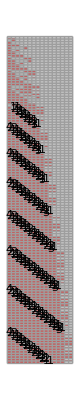

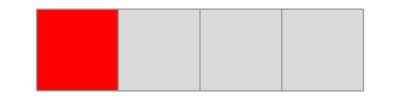
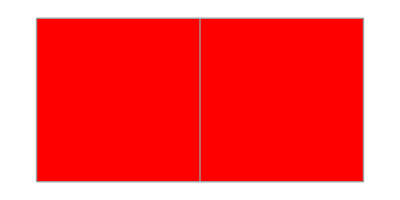

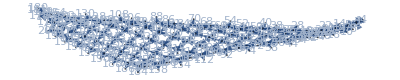
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSS[{"AA"->"","AB"->"BAAA","A"->"BB","B"->"A"},"A",200];
```

```mathematica
ToNetDifferenceSets[%100["Net"]]
```

{{1,2},{1},{1,1,2,3},{},{2,4},{1},{1,1,2,5},{},{1,1,2,4},{},{4,6},{1},{1,1,2,7},{},{1,1,2,6},{},{1,1,2,6},{},{6,8},{1},{1,1,2,9},{},{1,1,2,8},{},{1,1,2,8},{},{1,1,2,8},{},{8,10},{1},{1,1,2,11},{},{1,1,2,10},{},{1,1,2,10},{},{1,1,2,10},{},{1,1,2,10},{},{10,12},{1},{1,1,2,13},{},{1,1,2,12},{},{1,1,2,12},{},{1,1,2,12},{},{1,1,2,12},{},{1,1,2,12},{},{12,14},{1},{1,1,2,15},{},{1,1,2,14},{},{1,1,2,14},{},{1,1,2,14},{},{1,1,2,14},{},{1,1,2,14},{},{1,1,2,14},{},{14,16},{1},{1,1,2,17},{},{1,1,2,16},{},{1,1,2,16},{},{1,1,2,16},{},{1,1,2,16},{},{1,1,2,16},{},{1,1,2,16},{},{1,1,2,16},{},{16,18},{1},{1,1,2,19},{},{1,1,2,18},{},{1,1,2,18},{},{1,1,2,18},{},{1,1,2,18},{},{1,1,2,18},{},{1,1,2,18},{},{1,1,2,18},{},{1,1,2,18},{},{18,20},{1},{1,1,2,21},{},{1,1,2,20},{},{1,1,2,20},{},{1,1,2,20},{},{1,1,2,20},{},{1,1,2,20},{},{1,1,2,20},{},{1,1,2,20},{},{1,1,2,20},{},{1,1,2,20},{},{20,22},{1},{1,1,2,23},{},{1,1,2,22},{},{1,1,2,22},{},{1,1,2,22},{},{1,1,2,22},{},{1,1,2,22},{},{1,1,2,22},{},{1,1,2,22},{},{1,1,2,22},{},{1,1,2,22},{},{1,1,2,22},{},{22,24},{1},{1,1,2,25},{},{1,1,2,24},{},{1,1,2,24},{},{1,1,2,24},{},{1,1,2,24},{},{1,1,2,24},{},{1,1,2,24},{},{1,1,2,24},{},{1,1,2,24},{},{1,1,2,24},{},{1,1,2},{},{1,1,2},{},{},{1},{1,1,2},{},{1,1,2},{},{1,1,2},{},{1,1,2},{},{1,1,2},{},{1,1,2},{},{1,1,2},{},{1,1,2},{},{1,1}}

```mathematica
{{1,2},{1},{1,1,2,3},{},0·{{1,1,2,2},{}},
{2,4},{1},{1,1,2,5},{},1·{{1,1,2,4},{}},
{4,6},{1},{1,1,2,7},{},2·{{1,1,2,6},{}},
{6,8},{1},{1,1,2,9},{},3·{{1,1,2,8},{}},
{8,10},{1},{1,1,2,11},{},4·{{1,1,2,10},{}},
...}
```

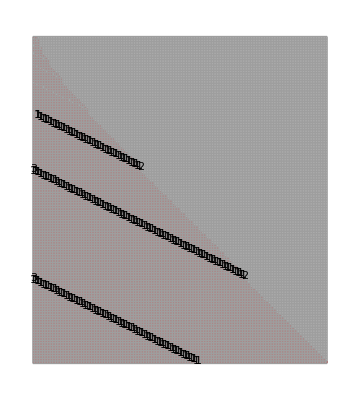
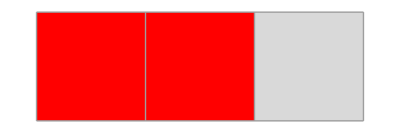
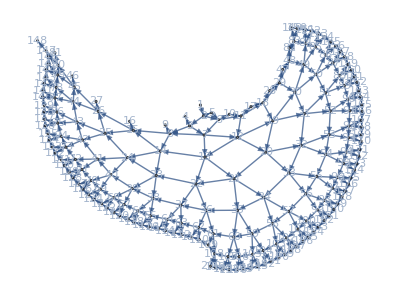
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sssEXP1=SSS[{"AB"->"BBA","A"->"","B"->"A"},"BBB",200];
```

```mathematica
ToNetDifferenceSets[sssEXP1["Net"]]
```

{{1},{1,3,4},{1,4,5},{},{1},{1,4,5},{1,5,6},{1,6,7},{},{1},{1,6,7},{1,7,8},{1,8,9},{1,9,10},{1,10,11},{},{1},{1,10,11},{1,11,12},{1,12,13},{1,13,14},{1,14,15},{1,15,16},{1,16,17},{1,17,18},{1,18,19},{},{1},{1,18,19},{1,19,20},{1,20,21},{1,21,22},{1,22,23},{1,23,24},{1,24,25},{1,25,26},{1,26,27},{1,27,28},{1,28,29},{1,29,30},{1,30,31},{1,31,32},{1,32,33},{1,33,34},{1,34,35},{},{1},{1,34,35},{1,35,36},{1,36,37},{1,37,38},{1,38,39},{1,39,40},{1,40,41},{1,41,42},{1,42,43},{1,43,44},{1,44,45},{1,45,46},{1,46,47},{1,47,48},{1,48,49},{1,49,50},{1,50,51},{1,51,52},{1,52,53},{1,53,54},{1,54,55},{1,55,56},{1,56,57},{1,57,58},{1,58,59},{1,59,60},{1,60,61},{1,61,62},{1,62,63},{1,63,64},{1,64,65},{1,65,66},{1,66,67},{},{1},{1,66,67},{1,67,68},{1,68,69},{1,69,70},{1,70,71},{1,71,72},{1,72,73},{1,73,74},{1,74,75},{1,75,76},{1,76,77},{1,77,78},{1,78,79},{1,79,80},{1,80,81},{1,81,82},{1,82,83},{1,83,84},{1,84,85},{1,85,86},{1,86,87},{1,87,88},{1,88,89},{1,89,90},{1,90,91},{1,91,92},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

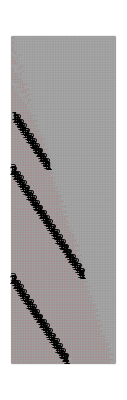
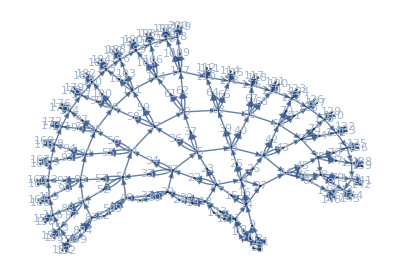
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sssEXP2=SSS[{"AA"->"B","AB"->"AAAAA","B"->"A"},"BB",200];
```

```mathematica
ToNetDifferenceSets[sssEXP2["Net"]]
```

{{1},{1,1,2,2,7},{2},{2},{1},{1,1,2,2,3},{3},{3},{5},{1},{1,1,2,2,3},{5},{5},{1,1,2,2,13},{6},{8},{1},{1,1,2,2,3},{9},{9},{1,1,2,2,3},{10},{12},{1,1,2,2,3},{13},{15},{17},{1},{1,1,2,2,3},{17},{17},{1,1,2,2,3},{18},{20},{1,1,2,2,3},{21},{23},{1,1,2,2,3},{24},{26},{1,1,2,2,3},{27},{29},{1,1,2,2,37},{30},{32},{1},{1,1,2,2,3},{33},{33},{1,1,2,2,3},{34},{36},{1,1,2,2,3},{37},{39},{1,1,2,2,3},{40},{42},{1,1,2,2,3},{43},{45},{1,1,2,2,3},{46},{48},{1,1,2,2,3},{49},{51},{1,1,2,2,3},{52},{54},{1,1,2,2,3},{55},{57},{1,1,2,2,3},{58},{60},{1,1,2,2,3},{61},{63},{65},{1},{1,1,2,2,3},{65},{65},{1,1,2,2,3},{66},{68},{1,1,2,2,3},{69},{71},{1,1,2,2,3},{72},{74},{1,1,2,2,3},{75},{77},{1,1,2,2,3},{78},{80},{1,1,2,2,3},{81},{83},{1,1,2,2,3},{84},{86},{1,1,2,2,3},{87},{89},{1,1,2,2,3},{},{},{1,1,2,2,3},{},{},{1,1,2,2,3},{},{},{1,1,2,2,3},{},{},{1,1,2,2,3},{},{},{1,1,2,2,3},{},{},{1,1,2,2,3},{},{},{1,1,2,2,3},{},{},{1,1,2,2,3},{},{},{1,1,2,2,3},{},{},{1,1,2,2,3},{},{},{1,1,2,2,3},{},{},{1,1,2,2},{},{},{1},{1,1,2,2,3},{},{},{1,1,2,2,3},{},{},{1,1,2,2,3},{},{},{1,1,2,2,3},{},{},{1,1,2,2,3},{},{},{1,1,2,2,3},{},{},{1,1,2,2,3},{},{},{1,1,2,2,3},{},{},{1,1,2,2,3},{},{},{1,1,2,2,3},{},{},{1,1,2,2,3},{},{},{1,1,2,2,3},{},{},{1,1,2,2,3},{},{},{1,1,2,2,3},{},{},{1,1,2,2,3},{},{},{1,1,2,2,3},{},{},{1,1,2,2}}

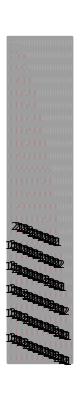
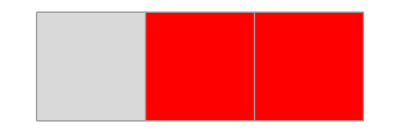

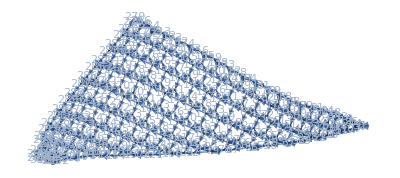
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sssEXP3=SSS[{"AA"->"AB","ABB"->"ABA","B"->"AA"},"B",300];
```

```mathematica
ToNetDifferenceSets[sssEXP3["Net"]]
```

{{1,1},{1,2},{1,4},{1,2},{1,2},{2,3},{3,4},{1,2},{3,4},{1,1},{3,4,5},{1,2},{4,5},{1,1},{1,4,5},{5,6},{1,2},{5,6},{1,1},{1,5,6},{1,1},{5,6,7},{1,2},{6,7},{1,1},{1,6,7},{1,1},{1,6,7},{7,8},{1,2},{7,8},{1,1},{1,7,8},{1,1},{1,7,8},{1,1},{7,8,9},{1,2},{8,9},{1,1},{1,8,9},{1,1},{1,8,9},{1,1},{1,8,9},{9,10},{1,2},{9,10},{1,1},{1,9,10},{1,1},{1,9,10},{1,1},{1,9,10},{1,1},{9,10,11},{1,2},{10,11},{1,1},{1,10,11},{1,1},{1,10,11},{1,1},{1,10,11},{1,1},{1,10,11},{11,12},{1,2},{11,12},{1,1},{1,11,12},{1,1},{1,11,12},{1,1},{1,11,12},{1,1},{1,11,12},{1,1},{11,12,13},{1,2},{12,13},{1,1},{1,12,13},{1,1},{1,12,13},{1,1},{1,12,13},{1,1},{1,12,13},{1,1},{1,12,13},{13,14},{1,2},{13,14},{1,1},{1,13,14},{1,1},{1,13,14},{1,1},{1,13,14},{1,1},{1,13,14},{1,1},{1,13,14},{1,1},{13,14,15},{1,2},{14,15},{1,1},{1,14,15},{1,1},{1,14,15},{1,1},{1,14,15},{1,1},{1,14,15},{1,1},{1,14,15},{1,1},{1,14,15},{15,16},{1,2},{15,16},{1,1},{1,15,16},{1,1},{1,15,16},{1,1},{1,15,16},{1,1},{1,15,16},{1,1},{1,15,16},{1,1},{1,15,16},{1,1},{15,16,17},{1,2},{16,17},{1,1},{1,16,17},{1,1},{1,16,17},{1,1},{1,16,17},{1,1},{1,16,17},{1,1},{1,16,17},{1,1},{1,16,17},{1,1},{1,16,17},{17,18},{1,2},{17,18},{1,1},{1,17,18},{1,1},{1,17,18},{1,1},{1,17,18},{1,1},{1,17,18},{1,1},{1,17,18},{1,1},{1,17,18},{1,1},{1,17,18},{1,1},{17,18,19},{1,2},{18,19},{1,1},{1,18,19},{1,1},{1,18,19},{1,1},{1,18,19},{1,1},{1,18,19},{1,1},{1,18,19},{1,1},{1,18,19},{1,1},{1,18,19},{1,1},{1,18,19},{19,20},{1,2},{19,20},{1,1},{1,19,20},{1,1},{1,19,20},{1,1},{1,19,20},{1,1},{1,19,20},{1,1},{1,19,20},{1,1},{1,19,20},{1,1},{1,19,20},{1,1},{1,19,20},{1,1},{19,20,21},{1,2},{20,21},{1,1},{1,20,21},{1,1},{1,20,21},{1,1},{1,20,21},{1,1},{1,20,21},{1,1},{1,20,21},{1,1},{1,20,21},{1,1},{1,20,21},{1,1},{1,20,21},{1,1},{1,20,21},{21,22},{1,2},{21,22},{1,1},{1,21,22},{1,1},{1,21,22},{1,1},{1,21,22},{1,1},{1,21,22},{1,1},{1,21,22},{1,1},{1,21,22},{1,1},{1,21,22},{1,1},{1,21,22},{1,1},{1,21,22},{1,1},{21,22,23},{1,2},{22,23},{1,1},{1,22,23},{1,1},{1,22,23},{1,1},{1,22,23},{1,1},{1,22,23},{1,1},{1,22,23},{1,1},{1,22,23},{1,1},{1,22,23},{1,1},{1,22,23},{1,1},{1,22,23},{1,1},{1,22,23},{23},{1,2},{},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1}}

```mathematica
e
```

```mathematica
{{1,1},{1,2},{1,4},{1,2},{1,2},{2,3},{3,4},{1,2},{3,4},
1·{{1,1},{3,4,5}},{1,2},{4,5},
1·{{1,1},{1,4,5}},{5,6},{1,2},{5,6},
1·{{1,1},{1,5,6}},{1,1},{5,6,7},{1,2},{6,7},
2·{{1,1},{1,6,7}},{7,8},{1,2},{7,8},2·{{1,1},{1,7,8}},{1,2},{8,9},
3·{{1,1},{1,8,9}},{9,10},{1,2},{9,10},3·{{1,1},{1,9,10}},{1,1},{9,10,11},{1,2},{10,11},
4·{{1,1},{1,10,11}},{11,12},{1,2},{11,12},4·{{1,1},{1,11,12}},{1,1},{11,12,13},{1,2},{12,13},
5·{{1,1},{1,12,13}},{13,14},{1,2},{13,14},5·{{1,1},{1,13,14}},{1,1},{13,14,15},{1,2},{14,15},
6·{{1,1},{1,14,15}},{15,16},{1,2},{15,16},6·{{1,1},{1,15,16}},{1,1},{15,16,17},{1,2},{16,17},
7·{{1,1},{1,16,17}},{17,18},{1,2},{17,18},7·{{1,1},{1,17,18}},{1,1},{17,18,19},{1,2},{18,19},
8·{{1,1},{1,18,19}},{19,20},{1,2},{19,20},8·{{1,1},{1,19,20}},{1,1},{19,20,21},{1,2},{20,21},
9·{{1,1},{1,20,21}},{21,22},{1,2},{21,22},9·{{1,1},{1,21,22}},{1,1},{21,22,23},{1,2},{22,23},
10·{{1,1},{1,22,23}},{23},{1,2}
```

```mathematica
ToReducedNetDifferenceSets[%]
```

$Aborted

```mathematica
{1·{{1,1}},1·{{1,2}},1·{{1,4}},1·{{1,2}},
1·{{1,2}},1·{{2,3}},    0·{{1,1},{1,2,3}},     1·{{3,4}},    1·{{1,2}},1·{{3,4}},     0·{{1,1},{1,3,4}},      1·{{1,1}},1·{{3,4,5}},       
1·{{1,2}},1·{{4,5}},    1·{{1,1},{1,4,5}},     1·{{5,6}},    1·{{1,2}},1·{{5,6}},     1·{{1,1},{1,5,6}},      1·{{1,1}},1·{{5,6,7}},       
1·{{1,2}},1·{{6,7}},    2·{{1,1},{1,6,7}},     1·{{7,8}},    1·{{1,2}},1·{{7,8}},     2·{{1,1},{1,7,8}},      1·{{1,1}},1·{{7,8,9}},       
1·{{1,2}},1·{{8,9}},    3·{{1,1},{1,8,9}},     1·{{9,10}},  1·{{1,2}},1·{{9,10}},  3·{{1,1},{1,9,10}},    1·{{1,1}},1·{{9,10,11}}, 
1·{{1,2}},1·{{10,11}},4·{{1,1},{1,10,11}},1·{{11,12}},1·{{1,2}},1·{{11,12}},4·{{1,1},{1,11,12}}, 1·{{1,1}},1·{{11,12,13}},
1·{{1,2}},1·{{12,13}},5·{{1,1},{1,12,13}},1·{{13,14}},1·{{1,2}},1·{{13,14}},5·{{1,1},{1,13,14}}, 1·{{1,1}},1·{{13,14,15}},
1·{{1,2}},1·{{14,15}},6·{{1,1},{1,14,15}},1·{{15,16}},1·{{1,2}},1·{{15,16}},6·{{1,1},{1,15,16}}, 1·{{1,1}},1·{{15,16,17}},
1·{{1,2}},1·{{16,17}},7·{{1,1},{1,16,17}},1·{{17,18}},1·{{1,2}},1·{{17,18}},7·{{1,1},{1,17,18}}, 1·{{1,1}},1·{{17,18,19}},
1·{{1,2}},1·{{18,19}},...}
```

Some summaries:

```mathematica
Underoverscript[𝕊, n=1, ∞][{1,1,1},{1,1,n},(n-2)·{{1,1,n+1}},{n+1,n+2}]
```

```mathematica
Underoverscript[𝕊, n=1, ∞][{1,1,n},(n-2)·{{1,1,n+1}},{n+1,n+2},{1,1,1}]
```

```mathematica
Underoverscript[𝕊, n=1, ∞][(n-2)·{{1,1,n+1}},{n+1,n+2},{1,1,1},{1,1,n+1}]
```

```mathematica
Underoverscript[𝕊, n=1, ∞][{n+1,n+2},{1,1,1},{1,1,n+1},(n-1)·{{1,1,n+2}}]
```

## NetSummary & NetSummarize algorithms

### Show Colton on 04.Feb.2022 (Tweaked on 02.Feb)

#### NetSummary:

```mathematica
Clear[NetSummary];
Format[NetSummary[x__, {var_, start_, finish_}]] :=
  DisplayForm[
   RowBox[{UnderoverscriptBox["𝕊", RowBox[{var, "=", start}], finish],
     "[", Sequence @@ Riffle[{x}, ","], "]"}]];
NetSummary /: Expand[NetSummary[x__, {var_, start_Integer, finish_Integer}]] :=
 Join @@ Table[{x}, {var, start, finish}];
NetSummary /: ExpandAll[NetSummary[x__, {var_, start_Integer, finish_Integer}]] :=
 Join @@ Table[{x}/.NetSummary[y___]:>Sequence@@(ExpandAll[NetSummary[y]]), {var, start, finish}]
```

```mathematica
NetSummary[
NetSummary[i·{{n(n+1)/2,n(n+1)/2+i,n(n+1)/2+i+1}},{i,1,n}],{n,1,∞}]
```

𝕊_(n=1)^∞[𝕊_(i=1)^n[i·{{1/2 n (n+1),i+1/2 n (n+1),i+1/2 n (n+1)+1}}]]

```mathematica
Expand@NetSummary[
NetSummary[i·{{n(n+1)/2,n(n+1)/2+i,n(n+1)/2+i+1}},{i,1,n}],{n,1,4}]
```

{𝕊_(i=1)^1[i·{{1,1+i,2+i}}],𝕊_(i=1)^2[i·{{3,3+i,4+i}}],𝕊_(i=1)^3[i·{{6,6+i,7+i}}],𝕊_(i=1)^4[i·{{10,10+i,11+i}}]}

```mathematica
ExpandAll @ NetSummary[
NetSummary[i·{{n(n+1)/2,n(n+1)/2+i,n(n+1)/2+i+1}},{i,1,n}],{n,1,4}]
```

{1·{{1,2,3}},1·{{3,4,5}},2·{{3,5,6}},1·{{6,7,8}},2·{{6,8,9}},3·{{6,9,10}},1·{{10,11,12}},2·{{10,12,13}},3·{{10,13,14}},4·{{10,14,15}}}

```mathematica
NetSummary[
NetSummary[
NetSummary[x·{n(n+1)(n+2)/6,n(n+1)(n+2)/6+x,n(n+1)(n+2)/6+x+1,n(n+1)(n+2)/6+x+2},{x,1,y}],{y,1,n}],{n,1,∞}]//TraditionalForm
```

𝕊_(n=1)^∞[𝕊_(y=1)^n[𝕊_(x=1)^y[x·{1/6 n (n+1) (n+2),1/6 n (n+1) (n+2)+x,1/6 n (n+1) (n+2)+x+1,1/6 n (n+1) (n+2)+x+2}]]]

```mathematica
ExpandAll @
NetSummary[
  NetSummary[
   NetSummary[x·{n (n + 1) (n + 2)/6, n (n + 1) (n + 2)/6 + x, n (n + 1) (n + 2)/6 + x + 1, n (n + 1) (n + 2)/6 + x + 2},
    {x, 1, y}],
   {y, 1, n}],
  {n, 1, 5}]   // Flatten[#,2]&
```

{1·{1,2,3,4},1·{4,5,6,7},1·{4,5,6,7},2·{4,6,7,8},1·{10,11,12,13},1·{10,11,12,13},2·{10,12,13,14},1·{10,11,12,13},2·{10,12,13,14},3·{10,13,14,15},1·{20,21,22,23},1·{20,21,22,23},2·{20,22,23,24},1·{20,21,22,23},2·{20,22,23,24},3·{20,23,24,25},1·{20,21,22,23},2·{20,22,23,24},3·{20,23,24,25},4·{20,24,25,26},1·{35,36,37,38},1·{35,36,37,38},2·{35,37,38,39},1·{35,36,37,38},2·{35,37,38,39},3·{35,38,39,40},1·{35,36,37,38},2·{35,37,38,39},3·{35,38,39,40},4·{35,39,40,41},1·{35,36,37,38},2·{35,37,38,39},3·{35,38,39,40},4·{35,39,40,41},5·{35,40,41,42}}

#### NetSummarize:

```mathematica
Clear[n]
```

```mathematica
lm={{1,1,1},{1,1,2},{3,4},{1,1,1},{1,1,3},1·{{1,1,4}},{4,5},{1,1,1},{1,1,4},2·{{1,1,5}},{5,6},{1,1,1},{1,1,5},3·{{1,1,6}},{6,7},{1,1,1},{1,1,6},4·{{1,1,7}},{7,8},{1,1,1},{1,1,7},{},5·{{1,1,8}},{8,9}};
```

```mathematica
NetSummarize[l:{((_·{___})|{___})..}] :=Module[{lpat,chunksize=1,lpatpart,lpatpartpairs,booletable={},goodness,maxrunlens,fracs,pos,goodchunks,intpos,ans,tail,theoreticaltail,i,j,n,term,fnlans},
lpat = (l /. _Integer->"i"); (* replace all integers by "i" *)
For[chunksize=1,chunksize<=Length[lpat]/4,chunksize++,  (* loop on viable chunksize *)
lpatpart=Partition[lpat,chunksize];
lpatpartpairs=Partition[lpatpart,2,1]; (* we will compare neighbors *)
AppendTo[booletable,Boole[SameQ @@@ lpatpartpairs]]  (* 1 = match, 0 = no match *)
];
Print@Grid@booletable;
goodness=Split/@booletable;    (* split each line into runs *)
(* Print[goodness]; *)
goodness=ReplaceAll[goodness,{x:{1..}:>Length[x],{0..}->0}];  (* count the runs of 1s, replace runs of 0s by a single 0 *)
(* Print[goodness]; *)
maxrunlens=Max /@ goodness;  (* find longest run of 1s in each row *)
Print[1+maxrunlens];  (* greatest number of matching chunks in each row *)
fracs=(If[#<2,0,#+1]&/@maxrunlens)^2/(1+Length/@ booletable);
(* Initial triage here, if <2 comparisons, i.e., if <3 matching chunks, replace by 0.  Max number of matches compared to possible number.  Later, after forward/backward extension, also count items in the original list and consider what fraction of the unreduced NetDifferenceSets list is explained. *)
Print[fracs];
chunksize=First@First@Position[fracs,Max[fracs]];
Print["best row / best chunk size: ",chunksize];
If[fracs[[chunksize]]<1,
Print["Unable to fit"];Print@Grid@booletable;Print[chunksize,": ",maxrunlens+1, ": ",fracs];
Return[]
];
pos={0,1}+First@SequencePosition[booletable[[chunksize]],{Repeated[1,{maxrunlens[[chunksize]]}]}];
Print[pos];
goodchunks=Partition[l,chunksize][[Span@@pos]]; (* these are the chunks to use *)
Print@Column[goodchunks];
intpos=GatherBy[Position[goodchunks,_Integer],Rest]; (* find & sort positions of integers *)
(* Print[intpos]; *)
(* Print[Extract[goodchunks,#]& /@ intpos]; *)
(* Print[FindSequenceFunction[Extract[goodchunks,#],n]& /@ intpos]; *)
(* Print[Thread[(First/@intpos)->(FindSequenceFunction[Extract[goodchunks,#],n]& /@ intpos)]]; *)
ans=First @ ReplacePart[goodchunks,Thread[(First/@intpos)->(FindSequenceFunction[Extract[goodchunks,#],ToExpression["n"]]& /@ intpos)]];

Print["ans: ",ans];
Print[NetSummary[Sequence@@ans,{ToExpression["n"],1,pos[[2]]-pos[[1]]+1}]];
Print[Expand@NetSummary[Sequence@@ans,{ToExpression["n"],1,pos[[2]]-pos[[1]]+1}]];
(* check validity of what we found *)
If[Flatten[goodchunks,1]!=Expand@NetSummary[Sequence@@ans,{ToExpression["n"],1,pos[[2]]-pos[[1]]+1}],
Print["Chunksize: ",chunksize];
Print@Flatten[goodchunks,1];
Print@Expand@NetSummary[Sequence@@ans,{ToExpression["n"],1,pos[[2]]-pos[[1]]+1}];
Print["Supposed match pattern: ",ans];
Return[]
];
Print["Checks out correctly for identified section"];
Print@NetSummary[Sequence@@ans,{ToExpression["n"],1,pos[[2]]-pos[[1]]+1}];

tail=l[[pos[[2]]*chunksize+1;;]];
If[Length[tail]>0,
theoreticaltail=Take[
Expand@NetSummary[Sequence@@ans,{ToExpression["n"],pos[[2]]-pos[[1]]+2,
pos[[2]]-pos[[1]]+2+(Ceiling[Length[l]/chunksize]-pos[[2]])}],
Length[tail]];
tailmatch=MapThread[Boole[SameQ[#1,#2]]&,{theoreticaltail,tail}]+
MapThread[Boole[SubsetQ[#1,#2]]&,{theoreticaltail,tail}];

Print["Length[tail] = ",Length[tail], " : ",tailmatch]
];

(* now try to extend backwards *)
i=(pos[[1]]-1)*chunksize; j=0;
(* just to the left of checked section in l, left (wrapping around) in pattern *)
While[i>0,
term=(ans[[Mod[j,chunksize,1]]] /. ToExpression["n"]->2-pos[[1]]+Quotient[i,chunksize,1]);
If[MatchQ[term,{___Integer}],
If[!(And@@(Positive/@term)),Break[]]; (* invalid prediction, quit loop *)
If[l[[i]]!=term,Break[]]  (* non-match, quit loop *)
];
If[MatchQ[term,(n_Integer /; n<0)·(_List)], Break[]];
If[MatchQ[term,0·(_List)],j--;Continue[]]; (* missing term ok *)
If[MatchQ[term,(_Integer)·{___List}] &&
 !(And@@(Positive/@Flatten[List@@term])), Break[]]; (* not all positive *)
If[l[[i]]!=term,Break[]];  (* non-match, quit *)
i--; j--];  (* back up until no match or i==0 (past beginning of list) *)
i++;j++;        (* step back to last actual match *)

Print["{i,j}=",{i,j}];
If[i==1,
Print["Match from beginning"],
Print["Initial non-matching terms: ",l[[;;i-1]]]
];

fnlans=ans;
Do[
fnlans=Prepend[Most[fnlans],(Last@fnlans)/. ToExpression["n"]->ToExpression["n-1"]],
1-j (* if j=0, do once, for j<0, repeat ... *)];


NetSummary[Sequence@@fnlans,{ToExpression["n"],1,Ceiling[(Length[l]-i+1)/chunksize]}]

];
NetSummarize[lm]
```

```mathematica
FindSequenceFunction[{2,4,8,16,32,64,128,256,512,1024},x]
```

2^x

```mathematica
FindSequenceFunction[{1,1,1,2,5,12,35,108,369},n]
```

```mathematica
FindSequenceFunction[{1,4,9,16,25},n]
```

n^2

```mathematica
FindSequenceFunction[{1,1,2,6,24,120,720,5040,40320,362880},n]
```

Pochhammer[1,-1+n]

```mathematica
Expand[%133]
```

{{1,1,1},{1,1,2},0·{{1,1,3}},{3,4},{1,1,1},{1,1,3},1·{{1,1,4}},{4,5},{1,1,1},{1,1,4},2·{{1,1,5}},{5,6},{1,1,1},{1,1,5},3·{{1,1,6}},{6,7},{1,1,1},{1,1,6},4·{{1,1,7}},{7,8},{1,1,1},{1,1,7},5·{{1,1,8}},{8,9}}

```mathematica
lm
```

{{1,1,1},{1,1,2},{3,4},{1,1,1},{1,1,3},1·{{1,1,4}},{4,5},{1,1,1},{1,1,4},2·{{1,1,5}},{5,6},{1,1,1},{1,1,5},3·{{1,1,6}},{6,7},{1,1,1},{1,1,6},4·{{1,1,7}},{7,8},{1,1,1},{1,1,7},5·{{1,1,8}},{8,9}}

```mathematica
%134==lm
```

False

```mathematica
NetSummary[{2+n,3+n},{1,1,1},{1,1,2+n},n·{{1,1,3+n}} ,{n,1,6}]
```

𝕊_(n=1)^6[{n+2,n+3},{1,1,1},{1,1,n+2},n·{{1,1,n+3}}]

```mathematica
Expand@NetSummary[{2+n,3+n},{1,1,1},{1,1,2+n},n·{{1,1,3+n}} ,{n,1,6}]
```

{{3,4},{1,1,1},{1,1,3},1·{{1,1,4}},{4,5},{1,1,1},{1,1,4},2·{{1,1,5}},{5,6},{1,1,1},{1,1,5},3·{{1,1,6}},{6,7},{1,1,1},{1,1,6},4·{{1,1,7}},{7,8},{1,1,1},{1,1,7},5·{{1,1,8}},{8,9},{1,1,1},{1,1,8},6·{{1,1,9}}}

If 1st entry rolls to the end, n->n+1
If last entry rolls to the beginning, n->n-1

```mathematica
Roll
```

```mathematica
Sort@Table[RotateLeft[{{2+n,3+n},{1,1,1},{1,1,2+n},n·{{1,1,3+n}}},k],{k,0,4-1}]
```

{{n·{{1,1,3+n}},{2+n,3+n},{1,1,1},{1,1,2+n}},{{2+n,3+n},{1,1,1},{1,1,2+n},n·{{1,1,3+n}}},{{1,1,1},{1,1,2+n},n·{{1,1,3+n}},{2+n,3+n}},{{1,1,2+n},n·{{1,1,3+n}},{2+n,3+n},{1,1,1}}}

```mathematica
Length/@ %37
```

{2,2,2,21,2}

```mathematica
SequenceMostLayer
```

```mathematica
data={{2,3},{1,1,1},{1,1,2},{3,4},{1,1,1},{1,1,3},1·{{1,1,4}},{4,5},{1,1,1},{1,1,4},2·{{1,1,5}},{5,6},{1,1,1},{1,1,5},3·{{1,1,6}},{6,7},{1,1,1},{1,1,6},4·{{1,1,7}},{7,8},{1,1,1},{42},{1,1,7},5·{{1,1,8}},{8,9},{1,1,1},{1,1,8},6·{{1,1,9}},{9,10},{1,1,1}};
```

```mathematica
NetSummarize[data]
```

0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 1 | 1 | 1 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

{2,1,2,4,1,1,1}

{0,0,0,16/7,0,0,0}

bestrow / best chunk size: 4

{2,5}

{{1,1,1},{1,1,3},1·{{1,1,4}},{4,5}}
{{1,1,1},{1,1,4},2·{{1,1,5}},{5,6}}
{{1,1,1},{1,1,5},3·{{1,1,6}},{6,7}}
{{1,1,1},{1,1,6},4·{{1,1,7}},{7,8}}

{{{1,1,1},{2,1,1},{3,1,1},{4,1,1}},{{1,1,2},{2,1,2},{3,1,2},{4,1,2}},{{1,1,3},{2,1,3},{3,1,3},{4,1,3}},{{1,2,1},{2,2,1},{3,2,1},{4,2,1}},{{1,2,2},{2,2,2},{3,2,2},{4,2,2}},{{1,2,3},{2,2,3},{3,2,3},{4,2,3}},{{1,3,1},{2,3,1},{3,3,1},{4,3,1}},{{1,3,2,1,1},{2,3,2,1,1},{3,3,2,1,1},{4,3,2,1,1}},{{1,3,2,1,2},{2,3,2,1,2},{3,3,2,1,2},{4,3,2,1,2}},{{1,3,2,1,3},{2,3,2,1,3},{3,3,2,1,3},{4,3,2,1,3}},{{1,4,1},{2,4,1},{3,4,1},{4,4,1}},{{1,4,2},{2,4,2},{3,4,2},{4,4,2}}}

{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1},{3,4,5,6},{1,2,3,4},{1,1,1,1},{1,1,1,1},{4,5,6,7},{4,5,6,7},{5,6,7,8}}

{1,1,1,1,1,2+n,n,1,1,3+n,3+n,4+n}

{{1,1,1}→1,{1,1,2}→1,{1,1,3}→1,{1,2,1}→1,{1,2,2}→1,{1,2,3}→2+n,{1,3,1}→n,{1,3,2,1,1}→1,{1,3,2,1,2}→1,{1,3,2,1,3}→3+n,{1,4,1}→3+n,{1,4,2}→4+n}

{{1,1,1},{1,1,2+n},n·{{1,1,3+n}},{3+n,4+n}}

𝕊_(n=1)^4[{1,1,1},{1,1,n+2},n·{{1,1,n+3}},{n+3,n+4}]

## 2022.Mar.04 HSC Research Lunch Program

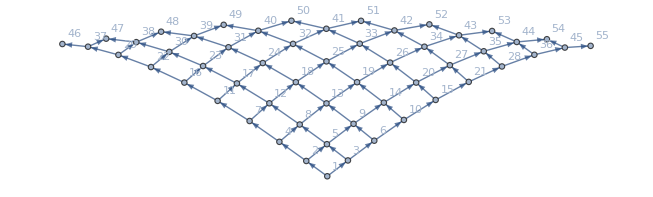

```mathematica
net2D={1->2,1->3,2->4,2->5,4->7,4->8,7->11,7->12,11->16,11->17,16->22,16->23,22->29,22->30,29->37,29->38,37->46,37->47,3->5,3->6,5->8,5->9,8->12,8->13,12->17,12->18,17->23,17->24,23->30,23->31,30->38,30->39,38->47,38->48,6->9,6->10,9->13,9->14,13->18,13->19,18->24,18->25,24->31,24->32,31->39,31->40,39->48,39->49,10->14,10->15,14->19,14->20,19->25,19->26,25->32,25->33,32->40,32->41,40->49,40->50,15->20,15->21,20->26,20->27,26->33,26->34,33->41,33->42,41->50,41->51,21->27,21->28,27->34,27->35,34->42,34->43,42->51,42->52,28->35,28->36,35->43,35->44,43->52,43->53,36->44,36->45,44->53,44->54,45->54,45->55}//Sort;
```

```mathematica
ToNetDifferenceSets[%]
```

{{1,2},{2,3},{2,3},{3,4},{3,4},{3,4},{4,5},{4,5},{4,5},{4,5},{5,6},{5,6},{5,6},{5,6},{5,6},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{7,8},{7,8},{7,8},{7,8},{7,8},{7,8},{7,8},{8,9},{8,9},{8,9},{8,9},{8,9},{8,9},{8,9},{8,9},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10}}

```mathematica
ToReducedNetDifferenceSets[%]
```

{{1,2},2·{{2,3}},3·{{3,4}},4·{{4,5}},5·{{5,6}},6·{{6,7}},7·{{7,8}},8·{{8,9}},9·{{9,10}}}

```mathematica
NetSummarize[%]
```

0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 |  |  |  |  |

{8,3}

{64/9,9/4}

best row / best chunk size: 1

{2,9}

{2·{{2,3}}}
{3·{{3,4}}}
{4·{{4,5}}}
{5·{{5,6}}}
{6·{{6,7}}}
{7·{{7,8}}}
{8·{{8,9}}}
{9·{{9,10}}}

ans: {(1+n)·{{1+n,2+n}}}

𝕊_(n=1)^8[(n+1)·{{n+1,n+2}}]

{2·{{2,3}},3·{{3,4}},4·{{4,5}},5·{{5,6}},6·{{6,7}},7·{{7,8}},8·{{8,9}},9·{{9,10}}}

Checks out correctly for identified section

𝕊_(n=1)^8[(1+n)·{{1+n,2+n}}]

{i,j}={1,0}

Match from beginning

𝕊_(n=1)^9[n·{{n,n+1}}]

```mathematica
NetSummary[n·{{n,n+1}},{n,1,5}]
```

𝕊_(n=1)^5[n·{{n,n+1}}]

```mathematica
ExpandAll[NetSummary[n·{{n,n+1}},{n,1,5}]]
```

{1·{{1,2}},2·{{2,3}},3·{{3,4}},4·{{4,5}},5·{{5,6}}}

```mathematica
FromReducedNetDifferenceSets[%6]
```

{{{1,2}},{{2,3}},{{2,3}},{{3,4}},{{3,4}},{{3,4}},{{4,5}},{{4,5}},{{4,5}},{{4,5}},{{5,6}},{{5,6}},{{5,6}},{{5,6}},{{5,6}}}

```mathematica
%3
```

{{1,2},2·{{2,3}},3·{{3,4}},4·{{4,5}},5·{{5,6}},6·{{6,7}},7·{{7,8}},8·{{8,9}},9·{{9,10}}}

#### The 3D-version

```mathematica
NetSummary[NetSummary[i·{{an=(1/2)n(n+1),an+i,an+i+1}},{i,1,n}],{n,1,∞}]
```

𝕊_(n=1)^∞[𝕊_(i=1)^n[i·{{1/2 n (1+n),i+1/2 n (1+n),1+i+1/2 n (1+n)}}]]

```mathematica
ExpandAll@NetSummary[NetSummary[i·{{an=1/2 n(n+1),an+i,an+i+1}},{i,1,n}],{n,1,5}]
```

{1·{{1,2,3}},1·{{3,4,5}},2·{{3,5,6}},1·{{6,7,8}},2·{{6,8,9}},3·{{6,9,10}},1·{{10,11,12}},2·{{10,12,13}},3·{{10,13,14}},4·{{10,14,15}},1·{{15,16,17}},2·{{15,17,18}},3·{{15,18,19}},4·{{15,19,20}},5·{{15,20,21}}}

```mathematica
ExpandAll@NetSummary[NetSummary[i·{{an=1/2 n(n+1),an+i,an+i+1}},{i,1,n}],{n,1,7}]
```

{1·{{1,2,3}},1·{{3,4,5}},2·{{3,5,6}},1·{{6,7,8}},2·{{6,8,9}},3·{{6,9,10}},1·{{10,11,12}},2·{{10,12,13}},3·{{10,13,14}},4·{{10,14,15}},1·{{15,16,17}},2·{{15,17,18}},3·{{15,18,19}},4·{{15,19,20}},5·{{15,20,21}},1·{{21,22,23}},2·{{21,23,24}},3·{{21,24,25}},4·{{21,25,26}},5·{{21,26,27}},6·{{21,27,28}},1·{{28,29,30}},2·{{28,30,31}},3·{{28,31,32}},4·{{28,32,33}},5·{{28,33,34}},6·{{28,34,35}},7·{{28,35,36}}}

```mathematica
NetSummary[{28,35,36},{n,1,7}]
```

𝕊_(n=1)^7[{28,35,36}]

```mathematica
NetSummarize[%]
```

1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1 | 1 | 1 | 1 | 1 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1 | 1 | 1 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1 | 1 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1 | 1 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

{28,14,9,7,5,4,4}

{28,14,9,7,5,4,4}

best row / best chunk size: 1

{1,28}

{1·{{1,2,3}}}
{1·{{3,4,5}}}
{2·{{3,5,6}}}
{1·{{6,7,8}}}
{2·{{6,8,9}}}
{3·{{6,9,10}}}
{1·{{10,11,12}}}
{2·{{10,12,13}}}
{3·{{10,13,14}}}
{4·{{10,14,15}}}
{1·{{15,16,17}}}
{2·{{15,17,18}}}
{3·{{15,18,19}}}
{4·{{15,19,20}}}
{5·{{15,20,21}}}
{1·{{21,22,23}}}
{2·{{21,23,24}}}
{3·{{21,24,25}}}
{4·{{21,25,26}}}
{5·{{21,26,27}}}
{6·{{21,27,28}}}
{1·{{28,29,30}}}
{2·{{28,30,31}}}
{3·{{28,31,32}}}
{4·{{28,32,33}}}
{5·{{28,33,34}}}
{6·{{28,34,35}}}
{7·{{28,35,36}}}

ans: {[n]·{{[n],[n],[n]}}}

𝕊_(n=1)^28[[n]·{{[n],[n],[n]}}]

{1·{{1,2,3}},1·{{3,4,5}},2·{{3,5,6}},1·{{6,7,8}},2·{{6,8,9}},3·{{6,9,10}},1·{{10,11,12}},2·{{10,12,13}},3·{{10,13,14}},4·{{10,14,15}},1·{{15,16,17}},2·{{15,17,18}},3·{{15,18,19}},4·{{15,19,20}},5·{{15,20,21}},1·{{21,22,23}},2·{{21,23,24}},3·{{21,24,25}},4·{{21,25,26}},5·{{21,26,27}},6·{{21,27,28}},1·{{28,29,30}},2·{{28,30,31}},3·{{28,31,32}},4·{{28,32,33}},5·{{28,33,34}},6·{{28,34,35}},7·{{28,35,36}}}

Checks out correctly for identified section

𝕊_(n=1)^28[[n]·{{[n],[n],[n]}}]

{i,j}={1,1}

Match from beginning

𝕊_(n=1)^28[[n]·{{[n],[n],[n]}}]

#### Compare to a 4D-version

```mathematica
NetSummary[
NetSummary[
NetSummary[x·{1/(3!)(n+2)(n+1)n,1/(3!)(n+2)(n+1)n+x,1/(3!)(n+2)(n+1)n+x+1,1/(3!)(n+2)(n+1)n+x+2},
{x,1,y}],
{y,1,n}],
{n,1,∞}]
```

𝕊_(n=1)^∞[𝕊_(y=1)^n[𝕊_(x=1)^y[x·{1/6 n (1+n) (2+n),1/6 n (1+n) (2+n)+x,1+1/6 n (1+n) (2+n)+x,2+1/6 n (1+n) (2+n)+x}]]]

```mathematica
ExpandAll[NetSummary[NetSummary[NetSummary[x·{{an=1/(3!)(n+2)(n+1)n,an+x,an+x+1,an+x+2}},{x,1,y}],{y,1,n}],{n,1,6}]]
```

{1·{{1,2,3,4}},1·{{4,5,6,7}},1·{{4,5,6,7}},2·{{4,6,7,8}},1·{{10,11,12,13}},1·{{10,11,12,13}},2·{{10,12,13,14}},1·{{10,11,12,13}},2·{{10,12,13,14}},3·{{10,13,14,15}},1·{{20,21,22,23}},1·{{20,21,22,23}},2·{{20,22,23,24}},1·{{20,21,22,23}},2·{{20,22,23,24}},3·{{20,23,24,25}},1·{{20,21,22,23}},2·{{20,22,23,24}},3·{{20,23,24,25}},4·{{20,24,25,26}},1·{{35,36,37,38}},1·{{35,36,37,38}},2·{{35,37,38,39}},1·{{35,36,37,38}},2·{{35,37,38,39}},3·{{35,38,39,40}},1·{{35,36,37,38}},2·{{35,37,38,39}},3·{{35,38,39,40}},4·{{35,39,40,41}},1·{{35,36,37,38}},2·{{35,37,38,39}},3·{{35,38,39,40}},4·{{35,39,40,41}},5·{{35,40,41,42}},1·{{56,57,58,59}},1·{{56,57,58,59}},2·{{56,58,59,60}},1·{{56,57,58,59}},2·{{56,58,59,60}},3·{{56,59,60,61}},1·{{56,57,58,59}},2·{{56,58,59,60}},3·{{56,59,60,61}},4·{{56,60,61,62}},1·{{56,57,58,59}},2·{{56,58,59,60}},3·{{56,59,60,61}},4·{{56,60,61,62}},5·{{56,61,62,63}},1·{{56,57,58,59}},2·{{56,58,59,60}},3·{{56,59,60,61}},4·{{56,60,61,62}},5·{{56,61,62,63}},6·{{56,62,63,64}}}

```mathematica
FromReducedNetDifferenceSets[%60]
```

{{1,2,3,4},{4,5,6,7},{4,5,6,7},{4,6,7,8},{4,6,7,8},{10,11,12,13},{10,11,12,13},{10,12,13,14},{10,12,13,14},{10,11,12,13},{10,12,13,14},{10,12,13,14},{10,13,14,15},{10,13,14,15},{10,13,14,15},{20,21,22,23},{20,21,22,23},{20,22,23,24},{20,22,23,24},{20,21,22,23},{20,22,23,24},{20,22,23,24},{20,23,24,25},{20,23,24,25},{20,23,24,25},{20,21,22,23},{20,22,23,24},{20,22,23,24},{20,23,24,25},{20,23,24,25},{20,23,24,25},{20,24,25,26},{20,24,25,26},{20,24,25,26},{20,24,25,26},{35,36,37,38},{35,36,37,38},{35,37,38,39},{35,37,38,39},{35,36,37,38},{35,37,38,39},{35,37,38,39},{35,38,39,40},{35,38,39,40},{35,38,39,40},{35,36,37,38},{35,37,38,39},{35,37,38,39},{35,38,39,40},{35,38,39,40},{35,38,39,40},{35,39,40,41},{35,39,40,41},{35,39,40,41},{35,39,40,41},{35,36,37,38},{35,37,38,39},{35,37,38,39},{35,38,39,40},{35,38,39,40},{35,38,39,40},{35,39,40,41},{35,39,40,41},{35,39,40,41},{35,39,40,41},{35,40,41,42},{35,40,41,42},{35,40,41,42},{35,40,41,42},{35,40,41,42},{56,57,58,59},{56,57,58,59},{56,58,59,60},{56,58,59,60},{56,57,58,59},{56,58,59,60},{56,58,59,60},{56,59,60,61},{56,59,60,61},{56,59,60,61},{56,57,58,59},{56,58,59,60},{56,58,59,60},{56,59,60,61},{56,59,60,61},{56,59,60,61},{56,60,61,62},{56,60,61,62},{56,60,61,62},{56,60,61,62},{56,57,58,59},{56,58,59,60},{56,58,59,60},{56,59,60,61},{56,59,60,61},{56,59,60,61},{56,60,61,62},{56,60,61,62},{56,60,61,62},{56,60,61,62},{56,61,62,63},{56,61,62,63},{56,61,62,63},{56,61,62,63},{56,61,62,63},{56,57,58,59},{56,58,59,60},{56,58,59,60},{56,59,60,61},{56,59,60,61},{56,59,60,61},{56,60,61,62},{56,60,61,62},{56,60,61,62},{56,60,61,62},{56,61,62,63},{56,61,62,63},{56,61,62,63},{56,61,62,63},{56,61,62,63},{56,62,63,64},{56,62,63,64},{56,62,63,64},{56,62,63,64},{56,62,63,64},{56,62,63,64}}

```mathematica
FromNetDifferenceSets[%63]
```

{1→2,1→3,1→4,1→5,2→6,2→7,2→8,2→9,3→7,3→8,3→9,3→10,4→8,4→10,4→11,4→12,5→9,5→11,5→12,5→13,6→16,6→17,6→18,6→19,7→17,7→18,7→19,7→20,8→18,8→20,8→21,8→22,9→19,9→21,9→22,9→23,10→20,10→21,10→22,10→23,11→21,11→23,11→24,11→25,12→22,12→24,12→25,12→26,13→23,13→26,13→27,13→28,14→24,14→27,14→28,14→29,15→25,15→28,15→29,15→30,16→36,16→37,16→38,16→39,17→37,17→38,17→39,17→40,18→38,18→40,18→41,18→42,19→39,19→41,19→42,19→43,20→40,20→41,20→42,20→43,21→41,21→43,21→44,21→45,22→42,22→44,22→45,22→46,23→43,23→46,23→47,23→48,24→44,24→47,24→48,24→49,25→45,25→48,25→49,25→50,26→46,26→47,26→48,26→49,27→47,27→49,27→50,27→51,28→48,28→50,28→51,28→52,29→49,29→52,29→53,29→54,30→50,30→53,30→54,30→55,31→51,31→54,31→55,31→56,32→52,32→56,32→57,32→58,33→53,33→57,33→58,33→59,34→54,34→58,34→59,34→60,35→55,35→59,35→60,35→61,36→71,36→72,36→73,36→74,37→72,37→73,37→74,37→75,38→73,38→75,38→76,38→77,39→74,39→76,39→77,39→78,40→75,40→76,40→77,40→78,41→76,41→78,41→79,41→80,42→77,42→79,42→80,42→81,43→78,43→81,43→82,43→83,44→79,44→82,44→83,44→84,45→80,45→83,45→84,45→85,46→81,46→82,46→83,46→84,47→82,47→84,47→85,47→86,48→83,48→85,48→86,48→87,49→84,49→87,49→88,49→89,50→85,50→88,50→89,50→90,51→86,51→89,51→90,51→91,52→87,52→91,52→92,52→93,53→88,53→92,53→93,53→94,54→89,54→93,54→94,54→95,55→90,55→94,55→95,55→96,56→91,56→92,56→93,56→94,57→92,57→94,57→95,57→96,58→93,58→95,58→96,58→97,59→94,59→97,59→98,59→99,60→95,60→98,60→99,60→100,61→96,61→99,61→100,61→101,62→97,62→101,62→102,62→103,63→98,63→102,63→103,63→104,64→99,64→103,64→104,64→105,65→100,65→104,65→105,65→106,66→101,66→106,66→107,66→108,67→102,67→107,67→108,67→109,68→103,68→108,68→109,68→110,69→104,69→109,69→110,69→111,70→105,70→110,70→111,70→112,71→127,71→128,71→129,71→130,72→128,72→129,72→130,72→131,73→129,73→131,73→132,73→133,74→130,74→132,74→133,74→134,75→131,75→132,75→133,75→134,76→132,76→134,76→135,76→136,77→133,77→135,77→136,77→137,78→134,78→137,78→138,78→139,79→135,79→138,79→139,79→140,80→136,80→139,80→140,80→141,81→137,81→138,81→139,81→140,82→138,82→140,82→141,82→142,83→139,83→141,83→142,83→143,84→140,84→143,84→144,84→145,85→141,85→144,85→145,85→146,86→142,86→145,86→146,86→147,87→143,87→147,87→148,87→149,88→144,88→148,88→149,88→150,89→145,89→149,89→150,89→151,90→146,90→150,90→151,90→152,91→147,91→148,91→149,91→150,92→148,92→150,92→151,92→152,93→149,93→151,93→152,93→153,94→150,94→153,94→154,94→155,95→151,95→154,95→155,95→156,96→152,96→155,96→156,96→157,97→153,97→157,97→158,97→159,98→154,98→158,98→159,98→160,99→155,99→159,99→160,99→161,100→156,100→160,100→161,100→162,101→157,101→162,101→163,101→164,102→158,102→163,102→164,102→165,103→159,103→164,103→165,103→166,104→160,104→165,104→166,104→167,105→161,105→166,105→167,105→168,106→162,106→163,106→164,106→165,107→163,107→165,107→166,107→167,108→164,108→166,108→167,108→168,109→165,109→168,109→169,109→170,110→166,110→169,110→170,110→171,111→167,111→170,111→171,111→172,112→168,112→172,112→173,112→174,113→169,113→173,113→174,113→175,114→170,114→174,114→175,114→176,115→171,115→175,115→176,115→177,116→172,116→177,116→178,116→179,117→173,117→178,117→179,117→180,118→174,118→179,118→180,118→181,119→175,119→180,119→181,119→182,120→176,120→181,120→182,120→183,121→177,121→183,121→184,121→185,122→178,122→184,122→185,122→186,123→179,123→185,123→186,123→187,124→180,124→186,124→187,124→188,125→181,125→187,125→188,125→189,126→182,126→188,126→189,126→190}

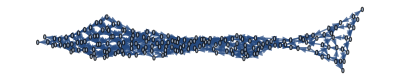

```mathematica
Graph[%]
```